# Effet Stark

```mathematica
Clear[]
Off[General::"spell1"]
<<"Units`"
<<"PhysicalConstants`"
$MaxPrecision=150;$MachinePrecision;$MaxExtraPrecision=150;$MaxMachineNumber;
```

### Rb^87 data and other constants

Natural constants

```mathematica
hbar=1.054571596*10^-34; (*Js, ref. Steck*)
Head[hbar];
SetPrecision[hbar,15]; (*to show hbar with 15 numbers*)
Precision[hbar] (*hbar is given in Machine Precision*);
h=hbar*2.*π;
Subscript[μ, 0]=4.*π*10^-7 ; (*N/A^2, exact, ref. Steck*)
c=2.99792458*10^8; (*m/s, exact, ref. Steck*)
Subscript[ϵ, 0]=(Subscript[μ, 0] c^2)^-1; (*F/m, exact, ref. Steck*)
Subscript[k, B]=1.3806503*10^-23 ;(*J/K, ref. Steck*)
Subscript[m, e]=9.10938188*10^-31 (*ElectronMass [kg], ref. Steck*);
Subscript[e, SI]=1.602176462*10^-19 (*ElectronCharge [C], ref. Steck*);
Subscript[e, cgs]=Subscript[e, SI]/(4.π Subscript[ϵ, 0])^(1/2);
Subscript[a, 0]=0.5291772083*10^-10; (*m , Bohr Radius, ref. Steck*)
hbar^2/(Subscript[m, e]*Subscript[e, cgs]^2) (*Subscript[a, 0] calculated*);
Subscript[e, cgs]^2/Subscript[a, 0]/Subscript[e, SI] (*atomic energy unit given in [eV=Subscript[e, SI] V]*)
Subscript[μ, B]=9.27400899*10^-24 ;(*J/T , Bohr Magneton, ref. Steck*)
u=1.66053873*10^-27 ;(*kg, Atomic mass unit , ref. Steck*)
α=Subscript[e, SI]^2/(hbar c 4. π Subscript[ϵ, 0]);
SetPrecision[α,9];
Subscript[R, ∞]=(α^2 Subscript[m, e] c)/(4.π hbar) ;(* Rydberg constant: Wikipedia Subscript[R, ∞]=1.0973731568525(73)*10^7 m^-1, slightly different from value calculated with constants from ref. Steck *) 

SetPrecision[Subscript[R, ∞],13] (*to show Subscript[R, ∞] with 13 numbers*)

(*Rubidium*)

Subscript[m, Rb87]=86.909180520*u; (*kg, Atomic Mass^87 Rb, ref. Steck*)
Subscript[R, Rb87]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb87])^-1 ;(* Subscript[R, Rb]=109736.605 cm^-1 from PRA 67 052502 (2003) Gallagher, "where R_Rb is the Rydberg constant for the reduced electron mass in Rb" -> obviously for Rb85 !! *)
SetPrecision[Subscript[R, Rb87],9] (*to show Subscript[R, ∞] with 9 numbers*)

Subscript[m, Rb85]=84.909180520*u; (*kg, Atomic Mass^85 Rb*)
Subscript[R, Rb85]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb85])^-1 ;
1-(1+Subscript[m, e]/Subscript[m, Rb85])^-1 (*relative effect of reduced mass (replacing Subscript[R, ∞] by Subscript[R, Rb87]) on Energy is in the order of 6E-6*)
Null
```

27.2114

1.09737315688×10^7

1.09736623×10^7

6.46074×10^-6

### Define Functions for calculation of energy-levels without interaction

Quantum defects taken from Publica
tion T. Gallagher et al. PRA 67, 052502 (2003), n>20. nf_j and ng_j states are found in Han, Gallagher et al. PRA 74 054502 (2006)

```mathematica
Subscript[δ, 0]={3.131145,2.65486,2.64165,1.34807,1.34642, 0.0165192,0.0165437,0};
Subscript[δ, 2]={0.195,0.280,0.318,-0.603,-0.545, -0.085,-0.086,0}; (*Meschede values*)

(*Subscript[δ, 0]={3.131804,2.6548849,2.6416737,1.34809171,1.34646572,0.0165192,0.0165437,0}
Subscript[δ, 2]={0.1784,0.2900,0.2950,-0.60286,-0.59600,-0.085,-0.086,0};*)
(*list of quantum defects for Rb85 et Rb87 from PRA 67, 052502 (2003) 1^st entry Subscript[ns, 1/2]: lj=1, 2^nd entry Subscript[np, 1/2]:lj=2,3^nd entry Subscript[np, 3/2]:lj=3, 4^th entry Subscript[nd, 3/2]: lj=4, 5^th entry Subscript[nd, 5/2]:lj=5, 6^th entry Subscript[nf, 5/2]:lj=6, 7^th entry Subscript[nf, 7/2]:lj=7,n>20, 8^th entry for levels with l>f quantum defect is set to zero*)

δ[lj_,n_]:=Subscript[δ, 0][[lj]]+(Subscript[δ, 2][[lj]])/(n-Subscript[δ, 0][[lj]])^2; (*Quantum defect for given lj and n for n>20, see T. Gallagher "Rydberg Atoms"*)
δ[7,41]

(*Energy of Rydberg levels with quantum defect (fine structure)*)

En[lj_,n_]:=-(Subscript[R, Rb87] c)/(n-δ[lj,n])^2 (*[Hz], Energy of Level |n,l,j> with quantum effect and mass correction *)
ERadinte[lj_,n_]:=-(0.5*(1+Subscript[m, e]/Subscript[m, Rb87])^-1)/(n-δ[lj,n])^2 (*[Unit=Atomic Energy Unit = Subscript[e, cgs]^2/Subscript[a, 0] [J] = 2 h Subscript[R, ∞] c [J] = 2*Subscript[E, Hydrogen n=1]], "Energy" as needed by "radinte.exe" of Level |n,l,j> with quantum defect and with reduced mass effect, n>20 *)
(*Effect of mass on Energylevels for Rb^87 and Rb^85*)

Enw85[lj_,n_]:=-(Subscript[R, Rb85] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb85 *)
SetPrecision[(Enw85[1,51]-Enw85[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb85 to control*);
Enw87[lj_,n_]:=-(Subscript[R, Rb87] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb87 *);
SetPrecision[(Enw87[1,51]-Enw87[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb87 to control*);
SetPrecision[(Enw87[1,51]-Enw87[1,50])-(Enw85[1,51]-Enw85[1,50]),15] (* Difference for Transition Frequencies in Hz for Rb87 and Rb85, effect in the order of 10kHz *)
```

0.0164925

7597.31420898438

### Integration of C-Code for Numerov Integration to calculate radial matrix elements, Tests of accuracy by comparison to Hydrogen

Install the external program "radinte.exe" which will be used to calculate the radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration in atomic length unit [a_0^I]   with the following Mathematica syntax: "RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer]".  l1 and l2 are magnetic quantum numbers. E1 and E2 are the Energies of the levels |n,l,j> calculated with quantum defect and with mass correction in atomic energy units ([e_cgs)^2/a_0] done by ERadinte[lj_,n_].
Attention: The Real numbers E1 and E2 have to be in floating point representation, otherwise Mathlink (communication between radinte.exe and Mathematica) will hang up!! The calculation in radinte.exe is done in double precision.

```mathematica
Install["D:\\Doktorarbeit\\Simus\\Mathematica\\radinte\\radinte\\Debug\\radinte.exe"]
?RadIntE

(*Test: Comparison with existing .exe file *)
RadIntE[
  ERadinte[1,50],-0.0453211,0,1,1]
RadIntE[-0.0453211,ERadinte[1,50],1,0,1]
RadIntE[-0.03661927,ERadinte[1,50],1,0,1]
Timing[RadIntE[-0.03661928,-0.0002276161,1,0,1]]
```

LinkObject["D:\Documents\raulcteixeira\Documents\Simulations et calculs\Simulation_Rydberg + taille du BEC dans piège magnétique\Spectres VdW\radinte\radinte.exe",8,8]

RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer] calculates radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration.

-0.0267757

-0.0267757

0.00739872

{0.,0.00741686}

## | 80 s1/2 >

#### Calculation of Interaction Matrix Elements <A,B|V_vdW|A',B'> centered at |60s1/2>

text

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=80;Subscript[l, 1]=0;Subscript[j, 1]=1/2;Subscript[m, 1]=1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=74; Subscript[n, max]=86;

δf=25*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Subscript[m, A]==1/2,t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

NList

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
```

-5.56765×10^11

{0.234,Null}

463

{{76,3,5/2,1/2,-5.69815×10^11,-1},{76,3,7/2,1/2,-5.69815×10^11,-1},{76,4,7/2,1/2,-5.69567×10^11,1},{76,4,9/2,1/2,-5.69567×10^11,1},{76,5,9/2,1/2,-5.69567×10^11,-1},{76,5,11/2,1/2,-5.69567×10^11,-1},{76,6,11/2,1/2,-5.69567×10^11,1},{76,6,13/2,1/2,-5.69567×10^11,1},{76,7,13/2,1/2,-5.69567×10^11,-1},{76,7,15/2,1/2,-5.69567×10^11,-1},{76,8,15/2,1/2,-5.69567×10^11,1},{76,8,17/2,1/2,-5.69567×10^11,1},{76,9,17/2,1/2,-5.69567×10^11,-1},{76,9,19/2,1/2,-5.69567×10^11,-1},{76,10,19/2,1/2,-5.69567×10^11,1},{76,10,21/2,1/2,-5.69567×10^11,1},{76,11,21/2,1/2,-5.69567×10^11,-1},{76,11,23/2,1/2,-5.69567×10^11,-1},{76,12,23/2,1/2,-5.69567×10^11,1},{76,12,25/2,1/2,-5.69567×10^11,1},{76,13,25/2,1/2,-5.69567×10^11,-1},{76,13,27/2,1/2,-5.69567×10^11,-1},{76,14,27/2,1/2,-5.69567×10^11,1},{76,14,29/2,1/2,-5.69567×10^11,1},{76,15,29/2,1/2,-5.69567×10^11,-1},{76,15,31/2,1/2,-5.69567×10^11,-1},{76,16,31/2,1/2,-5.69567×10^11,1},{76,16,33/2,1/2,-5.69567×10^11,1},{76,17,33/2,1/2,-5.69567×10^11,-1},{76,17,35/2,1/2,-5.69567×10^11,-1},{76,18,35/2,1/2,-5.69567×10^11,1},{76,18,37/2,1/2,-5.69567×10^11,1},{76,19,37/2,1/2,-5.69567×10^11,-1},{76,19,39/2,1/2,-5.69567×10^11,-1},{76,20,39/2,1/2,-5.69567×10^11,1},{76,20,41/2,1/2,-5.69567×10^11,1},{76,21,41/2,1/2,-5.69567×10^11,-1},{76,21,43/2,1/2,-5.69567×10^11,-1},{76,22,43/2,1/2,-5.69567×10^11,1},{76,22,45/2,1/2,-5.69567×10^11,1},{76,23,45/2,1/2,-5.69567×10^11,-1},{76,23,47/2,1/2,-5.69567×10^11,-1},{76,24,47/2,1/2,-5.69567×10^11,1},{76,24,49/2,1/2,-5.69567×10^11,1},{76,25,49/2,1/2,-5.69567×10^11,-1},{76,25,51/2,1/2,-5.69567×10^11,-1},{76,26,51/2,1/2,-5.69567×10^11,1},{76,26,53/2,1/2,-5.69567×10^11,1},{76,27,53/2,1/2,-5.69567×10^11,-1},{76,27,55/2,1/2,-5.69567×10^11,-1},{76,28,55/2,1/2,-5.69567×10^11,1},{76,28,57/2,1/2,-5.69567×10^11,1},{76,29,57/2,1/2,-5.69567×10^11,-1},{76,29,59/2,1/2,-5.69567×10^11,-1},{76,30,59/2,1/2,-5.69567×10^11,1},{76,30,61/2,1/2,-5.69567×10^11,1},{76,31,61/2,1/2,-5.69567×10^11,-1},{76,31,63/2,1/2,-5.69567×10^11,-1},{76,32,63/2,1/2,-5.69567×10^11,1},{76,32,65/2,1/2,-5.69567×10^11,1},{76,33,65/2,1/2,-5.69567×10^11,-1},{76,33,67/2,1/2,-5.69567×10^11,-1},{76,34,67/2,1/2,-5.69567×10^11,1},{76,34,69/2,1/2,-5.69567×10^11,1},{76,35,69/2,1/2,-5.69567×10^11,-1},{76,35,71/2,1/2,-5.69567×10^11,-1},{76,36,71/2,1/2,-5.69567×10^11,1},{76,36,73/2,1/2,-5.69567×10^11,1},{76,37,73/2,1/2,-5.69567×10^11,-1},{76,37,75/2,1/2,-5.69567×10^11,-1},{76,38,75/2,1/2,-5.69567×10^11,1},{76,38,77/2,1/2,-5.69567×10^11,1},{76,39,77/2,1/2,-5.69567×10^11,-1},{76,39,79/2,1/2,-5.69567×10^11,-1},{76,40,79/2,1/2,-5.69567×10^11,1},{76,40,81/2,1/2,-5.69567×10^11,1},{76,41,81/2,1/2,-5.69567×10^11,-1},{76,41,83/2,1/2,-5.69567×10^11,-1},{76,42,83/2,1/2,-5.69567×10^11,1},{76,42,85/2,1/2,-5.69567×10^11,1},{76,43,85/2,1/2,-5.69567×10^11,-1},{76,43,87/2,1/2,-5.69567×10^11,-1},{76,44,87/2,1/2,-5.69567×10^11,1},{76,44,89/2,1/2,-5.69567×10^11,1},{76,45,89/2,1/2,-5.69567×10^11,-1},{76,45,91/2,1/2,-5.69567×10^11,-1},{76,46,91/2,1/2,-5.69567×10^11,1},{76,46,93/2,1/2,-5.69567×10^11,1},{76,47,93/2,1/2,-5.69567×10^11,-1},{76,47,95/2,1/2,-5.69567×10^11,-1},{76,48,95/2,1/2,-5.69567×10^11,1},{76,48,97/2,1/2,-5.69567×10^11,1},{76,49,97/2,1/2,-5.69567×10^11,-1},{76,49,99/2,1/2,-5.69567×10^11,-1},{76,50,99/2,1/2,-5.69567×10^11,1},{76,50,101/2,1/2,-5.69567×10^11,1},{76,51,101/2,1/2,-5.69567×10^11,-1},{76,51,103/2,1/2,-5.69567×10^11,-1},{76,52,103/2,1/2,-5.69567×10^11,1},{76,52,105/2,1/2,-5.69567×10^11,1},{76,53,105/2,1/2,-5.69567×10^11,-1},{76,53,107/2,1/2,-5.69567×10^11,-1},{76,54,107/2,1/2,-5.69567×10^11,1},{76,54,109/2,1/2,-5.69567×10^11,1},{76,55,109/2,1/2,-5.69567×10^11,-1},{76,55,111/2,1/2,-5.69567×10^11,-1},{76,56,111/2,1/2,-5.69567×10^11,1},{76,56,113/2,1/2,-5.69567×10^11,1},{76,57,113/2,1/2,-5.69567×10^11,-1},{76,57,115/2,1/2,-5.69567×10^11,-1},{76,58,115/2,1/2,-5.69567×10^11,1},{76,58,117/2,1/2,-5.69567×10^11,1},{76,59,117/2,1/2,-5.69567×10^11,-1},{76,59,119/2,1/2,-5.69567×10^11,-1},{76,60,119/2,1/2,-5.69567×10^11,1},{76,60,121/2,1/2,-5.69567×10^11,1},{76,61,121/2,1/2,-5.69567×10^11,-1},{76,61,123/2,1/2,-5.69567×10^11,-1},{76,62,123/2,1/2,-5.69567×10^11,1},{76,62,125/2,1/2,-5.69567×10^11,1},{76,63,125/2,1/2,-5.69567×10^11,-1},{76,63,127/2,1/2,-5.69567×10^11,-1},{76,64,127/2,1/2,-5.69567×10^11,1},{76,64,129/2,1/2,-5.69567×10^11,1},{76,65,129/2,1/2,-5.69567×10^11,-1},{76,65,131/2,1/2,-5.69567×10^11,-1},{76,66,131/2,1/2,-5.69567×10^11,1},{76,66,133/2,1/2,-5.69567×10^11,1},{76,67,133/2,1/2,-5.69567×10^11,-1},{76,67,135/2,1/2,-5.69567×10^11,-1},{76,68,135/2,1/2,-5.69567×10^11,1},{76,68,137/2,1/2,-5.69567×10^11,1},{76,69,137/2,1/2,-5.69567×10^11,-1},{76,69,139/2,1/2,-5.69567×10^11,-1},{76,70,139/2,1/2,-5.69567×10^11,1},{76,70,141/2,1/2,-5.69567×10^11,1},{76,71,141/2,1/2,-5.69567×10^11,-1},{76,71,143/2,1/2,-5.69567×10^11,-1},{76,72,143/2,1/2,-5.69567×10^11,1},{76,72,145/2,1/2,-5.69567×10^11,1},{76,73,145/2,1/2,-5.69567×10^11,-1},{76,73,147/2,1/2,-5.69567×10^11,-1},{76,74,147/2,1/2,-5.69567×10^11,1},{76,74,149/2,1/2,-5.69567×10^11,1},{76,75,149/2,1/2,-5.69567×10^11,-1},{76,75,151/2,1/2,-5.69567×10^11,-1},{77,2,3/2,1/2,-5.74819×10^11,1},{77,2,5/2,1/2,-5.74794×10^11,1},{77,3,5/2,1/2,-5.55107×10^11,-1},{77,3,7/2,1/2,-5.55108×10^11,-1},{77,4,7/2,1/2,-5.54869×10^11,1},{77,4,9/2,1/2,-5.54869×10^11,1},{77,5,9/2,1/2,-5.54869×10^11,-1},{77,5,11/2,1/2,-5.54869×10^11,-1},{77,6,11/2,1/2,-5.54869×10^11,1},{77,6,13/2,1/2,-5.54869×10^11,1},{77,7,13/2,1/2,-5.54869×10^11,-1},{77,7,15/2,1/2,-5.54869×10^11,-1},{77,8,15/2,1/2,-5.54869×10^11,1},{77,8,17/2,1/2,-5.54869×10^11,1},{77,9,17/2,1/2,-5.54869×10^11,-1},{77,9,19/2,1/2,-5.54869×10^11,-1},{77,10,19/2,1/2,-5.54869×10^11,1},{77,10,21/2,1/2,-5.54869×10^11,1},{77,11,21/2,1/2,-5.54869×10^11,-1},{77,11,23/2,1/2,-5.54869×10^11,-1},{77,12,23/2,1/2,-5.54869×10^11,1},{77,12,25/2,1/2,-5.54869×10^11,1},{77,13,25/2,1/2,-5.54869×10^11,-1},{77,13,27/2,1/2,-5.54869×10^11,-1},{77,14,27/2,1/2,-5.54869×10^11,1},{77,14,29/2,1/2,-5.54869×10^11,1},{77,15,29/2,1/2,-5.54869×10^11,-1},{77,15,31/2,1/2,-5.54869×10^11,-1},{77,16,31/2,1/2,-5.54869×10^11,1},{77,16,33/2,1/2,-5.54869×10^11,1},{77,17,33/2,1/2,-5.54869×10^11,-1},{77,17,35/2,1/2,-5.54869×10^11,-1},{77,18,35/2,1/2,-5.54869×10^11,1},{77,18,37/2,1/2,-5.54869×10^11,1},{77,19,37/2,1/2,-5.54869×10^11,-1},{77,19,39/2,1/2,-5.54869×10^11,-1},{77,20,39/2,1/2,-5.54869×10^11,1},{77,20,41/2,1/2,-5.54869×10^11,1},{77,21,41/2,1/2,-5.54869×10^11,-1},{77,21,43/2,1/2,-5.54869×10^11,-1},{77,22,43/2,1/2,-5.54869×10^11,1},{77,22,45/2,1/2,-5.54869×10^11,1},{77,23,45/2,1/2,-5.54869×10^11,-1},{77,23,47/2,1/2,-5.54869×10^11,-1},{77,24,47/2,1/2,-5.54869×10^11,1},{77,24,49/2,1/2,-5.54869×10^11,1},{77,25,49/2,1/2,-5.54869×10^11,-1},{77,25,51/2,1/2,-5.54869×10^11,-1},{77,26,51/2,1/2,-5.54869×10^11,1},{77,26,53/2,1/2,-5.54869×10^11,1},{77,27,53/2,1/2,-5.54869×10^11,-1},{77,27,55/2,1/2,-5.54869×10^11,-1},{77,28,55/2,1/2,-5.54869×10^11,1},{77,28,57/2,1/2,-5.54869×10^11,1},{77,29,57/2,1/2,-5.54869×10^11,-1},{77,29,59/2,1/2,-5.54869×10^11,-1},{77,30,59/2,1/2,-5.54869×10^11,1},{77,30,61/2,1/2,-5.54869×10^11,1},{77,31,61/2,1/2,-5.54869×10^11,-1},{77,31,63/2,1/2,-5.54869×10^11,-1},{77,32,63/2,1/2,-5.54869×10^11,1},{77,32,65/2,1/2,-5.54869×10^11,1},{77,33,65/2,1/2,-5.54869×10^11,-1},{77,33,67/2,1/2,-5.54869×10^11,-1},{77,34,67/2,1/2,-5.54869×10^11,1},{77,34,69/2,1/2,-5.54869×10^11,1},{77,35,69/2,1/2,-5.54869×10^11,-1},{77,35,71/2,1/2,-5.54869×10^11,-1},{77,36,71/2,1/2,-5.54869×10^11,1},{77,36,73/2,1/2,-5.54869×10^11,1},{77,37,73/2,1/2,-5.54869×10^11,-1},{77,37,75/2,1/2,-5.54869×10^11,-1},{77,38,75/2,1/2,-5.54869×10^11,1},{77,38,77/2,1/2,-5.54869×10^11,1},{77,39,77/2,1/2,-5.54869×10^11,-1},{77,39,79/2,1/2,-5.54869×10^11,-1},{77,40,79/2,1/2,-5.54869×10^11,1},{77,40,81/2,1/2,-5.54869×10^11,1},{77,41,81/2,1/2,-5.54869×10^11,-1},{77,41,83/2,1/2,-5.54869×10^11,-1},{77,42,83/2,1/2,-5.54869×10^11,1},{77,42,85/2,1/2,-5.54869×10^11,1},{77,43,85/2,1/2,-5.54869×10^11,-1},{77,43,87/2,1/2,-5.54869×10^11,-1},{77,44,87/2,1/2,-5.54869×10^11,1},{77,44,89/2,1/2,-5.54869×10^11,1},{77,45,89/2,1/2,-5.54869×10^11,-1},{77,45,91/2,1/2,-5.54869×10^11,-1},{77,46,91/2,1/2,-5.54869×10^11,1},{77,46,93/2,1/2,-5.54869×10^11,1},{77,47,93/2,1/2,-5.54869×10^11,-1},{77,47,95/2,1/2,-5.54869×10^11,-1},{77,48,95/2,1/2,-5.54869×10^11,1},{77,48,97/2,1/2,-5.54869×10^11,1},{77,49,97/2,1/2,-5.54869×10^11,-1},{77,49,99/2,1/2,-5.54869×10^11,-1},{77,50,99/2,1/2,-5.54869×10^11,1},{77,50,101/2,1/2,-5.54869×10^11,1},{77,51,101/2,1/2,-5.54869×10^11,-1},{77,51,103/2,1/2,-5.54869×10^11,-1},{77,52,103/2,1/2,-5.54869×10^11,1},{77,52,105/2,1/2,-5.54869×10^11,1},{77,53,105/2,1/2,-5.54869×10^11,-1},{77,53,107/2,1/2,-5.54869×10^11,-1},{77,54,107/2,1/2,-5.54869×10^11,1},{77,54,109/2,1/2,-5.54869×10^11,1},{77,55,109/2,1/2,-5.54869×10^11,-1},{77,55,111/2,1/2,-5.54869×10^11,-1},{77,56,111/2,1/2,-5.54869×10^11,1},{77,56,113/2,1/2,-5.54869×10^11,1},{77,57,113/2,1/2,-5.54869×10^11,-1},{77,57,115/2,1/2,-5.54869×10^11,-1},{77,58,115/2,1/2,-5.54869×10^11,1},{77,58,117/2,1/2,-5.54869×10^11,1},{77,59,117/2,1/2,-5.54869×10^11,-1},{77,59,119/2,1/2,-5.54869×10^11,-1},{77,60,119/2,1/2,-5.54869×10^11,1},{77,60,121/2,1/2,-5.54869×10^11,1},{77,61,121/2,1/2,-5.54869×10^11,-1},{77,61,123/2,1/2,-5.54869×10^11,-1},{77,62,123/2,1/2,-5.54869×10^11,1},{77,62,125/2,1/2,-5.54869×10^11,1},{77,63,125/2,1/2,-5.54869×10^11,-1},{77,63,127/2,1/2,-5.54869×10^11,-1},{77,64,127/2,1/2,-5.54869×10^11,1},{77,64,129/2,1/2,-5.54869×10^11,1},{77,65,129/2,1/2,-5.54869×10^11,-1},{77,65,131/2,1/2,-5.54869×10^11,-1},{77,66,131/2,1/2,-5.54869×10^11,1},{77,66,133/2,1/2,-5.54869×10^11,1},{77,67,133/2,1/2,-5.54869×10^11,-1},{77,67,135/2,1/2,-5.54869×10^11,-1},{77,68,135/2,1/2,-5.54869×10^11,1},{77,68,137/2,1/2,-5.54869×10^11,1},{77,69,137/2,1/2,-5.54869×10^11,-1},{77,69,139/2,1/2,-5.54869×10^11,-1},{77,70,139/2,1/2,-5.54869×10^11,1},{77,70,141/2,1/2,-5.54869×10^11,1},{77,71,141/2,1/2,-5.54869×10^11,-1},{77,71,143/2,1/2,-5.54869×10^11,-1},{77,72,143/2,1/2,-5.54869×10^11,1},{77,72,145/2,1/2,-5.54869×10^11,1},{77,73,145/2,1/2,-5.54869×10^11,-1},{77,73,147/2,1/2,-5.54869×10^11,-1},{77,74,147/2,1/2,-5.54869×10^11,1},{77,74,149/2,1/2,-5.54869×10^11,1},{77,75,149/2,1/2,-5.54869×10^11,-1},{77,75,151/2,1/2,-5.54869×10^11,-1},{77,76,151/2,1/2,-5.54869×10^11,1},{77,76,153/2,1/2,-5.54869×10^11,1},{78,1,1/2,1/2,-5.79512×10^11,-1},{78,1,3/2,1/2,-5.79309×10^11,-1},{78,2,3/2,1/2,-5.59919×10^11,1},{78,2,5/2,1/2,-5.59895×10^11,1},{78,3,5/2,1/2,-5.40962×10^11,-1},{78,3,7/2,1/2,-5.40963×10^11,-1},{78,4,7/2,1/2,-5.40733×10^11,1},{78,4,9/2,1/2,-5.40733×10^11,1},{78,5,9/2,1/2,-5.40733×10^11,-1},{78,5,11/2,1/2,-5.40733×10^11,-1},{78,6,11/2,1/2,-5.40733×10^11,1},{78,6,13/2,1/2,-5.40733×10^11,1},{78,7,13/2,1/2,-5.40733×10^11,-1},{78,7,15/2,1/2,-5.40733×10^11,-1},{78,8,15/2,1/2,-5.40733×10^11,1},{78,8,17/2,1/2,-5.40733×10^11,1},{78,9,17/2,1/2,-5.40733×10^11,-1},{78,9,19/2,1/2,-5.40733×10^11,-1},{78,10,19/2,1/2,-5.40733×10^11,1},{78,10,21/2,1/2,-5.40733×10^11,1},{78,11,21/2,1/2,-5.40733×10^11,-1},{78,11,23/2,1/2,-5.40733×10^11,-1},{78,12,23/2,1/2,-5.40733×10^11,1},{78,12,25/2,1/2,-5.40733×10^11,1},{78,13,25/2,1/2,-5.40733×10^11,-1},{78,13,27/2,1/2,-5.40733×10^11,-1},{78,14,27/2,1/2,-5.40733×10^11,1},{78,14,29/2,1/2,-5.40733×10^11,1},{78,15,29/2,1/2,-5.40733×10^11,-1},{78,15,31/2,1/2,-5.40733×10^11,-1},{78,16,31/2,1/2,-5.40733×10^11,1},{78,16,33/2,1/2,-5.40733×10^11,1},{78,17,33/2,1/2,-5.40733×10^11,-1},{78,17,35/2,1/2,-5.40733×10^11,-1},{78,18,35/2,1/2,-5.40733×10^11,1},{78,18,37/2,1/2,-5.40733×10^11,1},{78,19,37/2,1/2,-5.40733×10^11,-1},{78,19,39/2,1/2,-5.40733×10^11,-1},{78,20,39/2,1/2,-5.40733×10^11,1},{78,20,41/2,1/2,-5.40733×10^11,1},{78,21,41/2,1/2,-5.40733×10^11,-1},{78,21,43/2,1/2,-5.40733×10^11,-1},{78,22,43/2,1/2,-5.40733×10^11,1},{78,22,45/2,1/2,-5.40733×10^11,1},{78,23,45/2,1/2,-5.40733×10^11,-1},{78,23,47/2,1/2,-5.40733×10^11,-1},{78,24,47/2,1/2,-5.40733×10^11,1},{78,24,49/2,1/2,-5.40733×10^11,1},{78,25,49/2,1/2,-5.40733×10^11,-1},{78,25,51/2,1/2,-5.40733×10^11,-1},{78,26,51/2,1/2,-5.40733×10^11,1},{78,26,53/2,1/2,-5.40733×10^11,1},{78,27,53/2,1/2,-5.40733×10^11,-1},{78,27,55/2,1/2,-5.40733×10^11,-1},{78,28,55/2,1/2,-5.40733×10^11,1},{78,28,57/2,1/2,-5.40733×10^11,1},{78,29,57/2,1/2,-5.40733×10^11,-1},{78,29,59/2,1/2,-5.40733×10^11,-1},{78,30,59/2,1/2,-5.40733×10^11,1},{78,30,61/2,1/2,-5.40733×10^11,1},{78,31,61/2,1/2,-5.40733×10^11,-1},{78,31,63/2,1/2,-5.40733×10^11,-1},{78,32,63/2,1/2,-5.40733×10^11,1},{78,32,65/2,1/2,-5.40733×10^11,1},{78,33,65/2,1/2,-5.40733×10^11,-1},{78,33,67/2,1/2,-5.40733×10^11,-1},{78,34,67/2,1/2,-5.40733×10^11,1},{78,34,69/2,1/2,-5.40733×10^11,1},{78,35,69/2,1/2,-5.40733×10^11,-1},{78,35,71/2,1/2,-5.40733×10^11,-1},{78,36,71/2,1/2,-5.40733×10^11,1},{78,36,73/2,1/2,-5.40733×10^11,1},{78,37,73/2,1/2,-5.40733×10^11,-1},{78,37,75/2,1/2,-5.40733×10^11,-1},{78,38,75/2,1/2,-5.40733×10^11,1},{78,38,77/2,1/2,-5.40733×10^11,1},{78,39,77/2,1/2,-5.40733×10^11,-1},{78,39,79/2,1/2,-5.40733×10^11,-1},{78,40,79/2,1/2,-5.40733×10^11,1},{78,40,81/2,1/2,-5.40733×10^11,1},{78,41,81/2,1/2,-5.40733×10^11,-1},{78,41,83/2,1/2,-5.40733×10^11,-1},{78,42,83/2,1/2,-5.40733×10^11,1},{78,42,85/2,1/2,-5.40733×10^11,1},{78,43,85/2,1/2,-5.40733×10^11,-1},{78,43,87/2,1/2,-5.40733×10^11,-1},{78,44,87/2,1/2,-5.40733×10^11,1},{78,44,89/2,1/2,-5.40733×10^11,1},{78,45,89/2,1/2,-5.40733×10^11,-1},{78,45,91/2,1/2,-5.40733×10^11,-1},{78,46,91/2,1/2,-5.40733×10^11,1},{78,46,93/2,1/2,-5.40733×10^11,1},{78,47,93/2,1/2,-5.40733×10^11,-1},{78,47,95/2,1/2,-5.40733×10^11,-1},{78,48,95/2,1/2,-5.40733×10^11,1},{78,48,97/2,1/2,-5.40733×10^11,1},{78,49,97/2,1/2,-5.40733×10^11,-1},{78,49,99/2,1/2,-5.40733×10^11,-1},{78,50,99/2,1/2,-5.40733×10^11,1},{78,50,101/2,1/2,-5.40733×10^11,1},{78,51,101/2,1/2,-5.40733×10^11,-1},{78,51,103/2,1/2,-5.40733×10^11,-1},{78,52,103/2,1/2,-5.40733×10^11,1},{78,52,105/2,1/2,-5.40733×10^11,1},{78,53,105/2,1/2,-5.40733×10^11,-1},{78,53,107/2,1/2,-5.40733×10^11,-1},{78,54,107/2,1/2,-5.40733×10^11,1},{78,54,109/2,1/2,-5.40733×10^11,1},{78,55,109/2,1/2,-5.40733×10^11,-1},{78,55,111/2,1/2,-5.40733×10^11,-1},{78,56,111/2,1/2,-5.40733×10^11,1},{78,56,113/2,1/2,-5.40733×10^11,1},{78,57,113/2,1/2,-5.40733×10^11,-1},{78,57,115/2,1/2,-5.40733×10^11,-1},{78,58,115/2,1/2,-5.40733×10^11,1},{78,58,117/2,1/2,-5.40733×10^11,1},{78,59,117/2,1/2,-5.40733×10^11,-1},{78,59,119/2,1/2,-5.40733×10^11,-1},{78,60,119/2,1/2,-5.40733×10^11,1},{78,60,121/2,1/2,-5.40733×10^11,1},{78,61,121/2,1/2,-5.40733×10^11,-1},{78,61,123/2,1/2,-5.40733×10^11,-1},{78,62,123/2,1/2,-5.40733×10^11,1},{78,62,125/2,1/2,-5.40733×10^11,1},{78,63,125/2,1/2,-5.40733×10^11,-1},{78,63,127/2,1/2,-5.40733×10^11,-1},{78,64,127/2,1/2,-5.40733×10^11,1},{78,64,129/2,1/2,-5.40733×10^11,1},{78,65,129/2,1/2,-5.40733×10^11,-1},{78,65,131/2,1/2,-5.40733×10^11,-1},{78,66,131/2,1/2,-5.40733×10^11,1},{78,66,133/2,1/2,-5.40733×10^11,1},{78,67,133/2,1/2,-5.40733×10^11,-1},{78,67,135/2,1/2,-5.40733×10^11,-1},{78,68,135/2,1/2,-5.40733×10^11,1},{78,68,137/2,1/2,-5.40733×10^11,1},{78,69,137/2,1/2,-5.40733×10^11,-1},{78,69,139/2,1/2,-5.40733×10^11,-1},{78,70,139/2,1/2,-5.40733×10^11,1},{78,70,141/2,1/2,-5.40733×10^11,1},{78,71,141/2,1/2,-5.40733×10^11,-1},{78,71,143/2,1/2,-5.40733×10^11,-1},{78,72,143/2,1/2,-5.40733×10^11,1},{78,72,145/2,1/2,-5.40733×10^11,1},{78,73,145/2,1/2,-5.40733×10^11,-1},{78,73,147/2,1/2,-5.40733×10^11,-1},{78,74,147/2,1/2,-5.40733×10^11,1},{78,74,149/2,1/2,-5.40733×10^11,1},{78,75,149/2,1/2,-5.40733×10^11,-1},{78,75,151/2,1/2,-5.40733×10^11,-1},{78,76,151/2,1/2,-5.40733×10^11,1},{78,76,153/2,1/2,-5.40733×10^11,1},{78,77,153/2,1/2,-5.40733×10^11,-1},{78,77,155/2,1/2,-5.40733×10^11,-1},{79,0,1/2,1/2,-5.71539×10^11,1},{79,1,1/2,1/2,-5.6443×10^11,-1},{79,1,3/2,1/2,-5.64235×10^11,-1},{79,2,3/2,1/2,-5.4559×10^11,1},{79,2,5/2,1/2,-5.45567×10^11,1},{80,0,1/2,1/2,-5.56765×10^11,1},{80,1,1/2,1/2,-5.49929×10^11,-1},{80,1,3/2,1/2,-5.49741×10^11,-1},{80,2,3/2,1/2,-5.31805×10^11,1},{80,2,5/2,1/2,-5.31783×10^11,1},{81,0,1/2,1/2,-5.42557×10^11,1},{81,1,1/2,1/2,-5.3598×10^11,-1},{81,1,3/2,1/2,-5.35799×10^11,-1}}

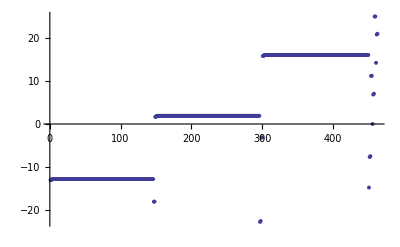

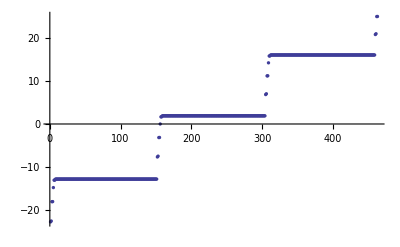

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;
LabelList

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);


EMatrixelement[{60,0,1/2,1/2},{63,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{62,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{61,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{60,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{59,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{58,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{57,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{56,1,1/2,-1/2}]


(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
EMatrix[[1,1]]
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]
```

{78|1|1/2|1/2,78|1|3/2|1/2,77|2|3/2|1/2,77|2|5/2|1/2,79|0|1/2|1/2,76|3|7/2|1/2,76|3|5/2|1/2,76|4|7/2|1/2,76|4|9/2|1/2,76|5|9/2|1/2,76|5|11/2|1/2,76|6|11/2|1/2,76|6|13/2|1/2,76|7|13/2|1/2,76|7|15/2|1/2,76|8|15/2|1/2,76|8|17/2|1/2,76|9|17/2|1/2,76|9|19/2|1/2,76|10|19/2|1/2,76|10|21/2|1/2,76|11|21/2|1/2,76|11|23/2|1/2,76|12|23/2|1/2,76|12|25/2|1/2,76|13|25/2|1/2,76|13|27/2|1/2,76|14|27/2|1/2,76|14|29/2|1/2,76|15|29/2|1/2,76|15|31/2|1/2,76|16|31/2|1/2,76|16|33/2|1/2,76|17|33/2|1/2,76|17|35/2|1/2,76|18|35/2|1/2,76|18|37/2|1/2,76|19|37/2|1/2,76|19|39/2|1/2,76|20|39/2|1/2,76|20|41/2|1/2,76|21|41/2|1/2,76|21|43/2|1/2,76|22|43/2|1/2,76|22|45/2|1/2,76|23|45/2|1/2,76|23|47/2|1/2,76|24|47/2|1/2,76|24|49/2|1/2,76|25|49/2|1/2,76|25|51/2|1/2,76|26|51/2|1/2,76|26|53/2|1/2,76|27|53/2|1/2,76|27|55/2|1/2,76|28|55/2|1/2,76|28|57/2|1/2,76|29|57/2|1/2,76|29|59/2|1/2,76|30|59/2|1/2,76|30|61/2|1/2,76|31|61/2|1/2,76|31|63/2|1/2,76|32|63/2|1/2,76|32|65/2|1/2,76|33|65/2|1/2,76|33|67/2|1/2,76|34|67/2|1/2,76|34|69/2|1/2,76|35|69/2|1/2,76|35|71/2|1/2,76|36|71/2|1/2,76|36|73/2|1/2,76|37|73/2|1/2,76|37|75/2|1/2,76|38|75/2|1/2,76|38|77/2|1/2,76|39|77/2|1/2,76|39|79/2|1/2,76|40|79/2|1/2,76|40|81/2|1/2,76|41|81/2|1/2,76|41|83/2|1/2,76|42|83/2|1/2,76|42|85/2|1/2,76|43|85/2|1/2,76|43|87/2|1/2,76|44|87/2|1/2,76|44|89/2|1/2,76|45|89/2|1/2,76|45|91/2|1/2,76|46|91/2|1/2,76|46|93/2|1/2,76|47|93/2|1/2,76|47|95/2|1/2,76|48|95/2|1/2,76|48|97/2|1/2,76|49|97/2|1/2,76|49|99/2|1/2,76|50|99/2|1/2,76|50|101/2|1/2,76|51|101/2|1/2,76|51|103/2|1/2,76|52|103/2|1/2,76|52|105/2|1/2,76|53|105/2|1/2,76|53|107/2|1/2,76|54|107/2|1/2,76|54|109/2|1/2,76|55|109/2|1/2,76|55|111/2|1/2,76|56|111/2|1/2,76|56|113/2|1/2,76|57|113/2|1/2,76|57|115/2|1/2,76|58|115/2|1/2,76|58|117/2|1/2,76|59|117/2|1/2,76|59|119/2|1/2,76|60|119/2|1/2,76|60|121/2|1/2,76|61|121/2|1/2,76|61|123/2|1/2,76|62|123/2|1/2,76|62|125/2|1/2,76|63|125/2|1/2,76|63|127/2|1/2,76|64|127/2|1/2,76|64|129/2|1/2,76|65|129/2|1/2,76|65|131/2|1/2,76|66|131/2|1/2,76|66|133/2|1/2,76|67|133/2|1/2,76|67|135/2|1/2,76|68|135/2|1/2,76|68|137/2|1/2,76|69|137/2|1/2,76|69|139/2|1/2,76|70|139/2|1/2,76|70|141/2|1/2,76|71|141/2|1/2,76|71|143/2|1/2,76|72|143/2|1/2,76|72|145/2|1/2,76|73|145/2|1/2,76|73|147/2|1/2,76|74|147/2|1/2,76|74|149/2|1/2,76|75|149/2|1/2,76|75|151/2|1/2,79|1|1/2|1/2,79|1|3/2|1/2,78|2|3/2|1/2,78|2|5/2|1/2,80|0|1/2|1/2,77|3|7/2|1/2,77|3|5/2|1/2,77|4|7/2|1/2,77|4|9/2|1/2,77|5|9/2|1/2,77|5|11/2|1/2,77|6|11/2|1/2,77|6|13/2|1/2,77|7|13/2|1/2,77|7|15/2|1/2,77|8|15/2|1/2,77|8|17/2|1/2,77|9|17/2|1/2,77|9|19/2|1/2,77|10|19/2|1/2,77|10|21/2|1/2,77|11|21/2|1/2,77|11|23/2|1/2,77|12|23/2|1/2,77|12|25/2|1/2,77|13|25/2|1/2,77|13|27/2|1/2,77|14|27/2|1/2,77|14|29/2|1/2,77|15|29/2|1/2,77|15|31/2|1/2,77|16|31/2|1/2,77|16|33/2|1/2,77|17|33/2|1/2,77|17|35/2|1/2,77|18|35/2|1/2,77|18|37/2|1/2,77|19|37/2|1/2,77|19|39/2|1/2,77|20|39/2|1/2,77|20|41/2|1/2,77|21|41/2|1/2,77|21|43/2|1/2,77|22|43/2|1/2,77|22|45/2|1/2,77|23|45/2|1/2,77|23|47/2|1/2,77|24|47/2|1/2,77|24|49/2|1/2,77|25|49/2|1/2,77|25|51/2|1/2,77|26|51/2|1/2,77|26|53/2|1/2,77|27|53/2|1/2,77|27|55/2|1/2,77|28|55/2|1/2,77|28|57/2|1/2,77|29|57/2|1/2,77|29|59/2|1/2,77|30|59/2|1/2,77|30|61/2|1/2,77|31|61/2|1/2,77|31|63/2|1/2,77|32|63/2|1/2,77|32|65/2|1/2,77|33|65/2|1/2,77|33|67/2|1/2,77|34|67/2|1/2,77|34|69/2|1/2,77|35|69/2|1/2,77|35|71/2|1/2,77|36|71/2|1/2,77|36|73/2|1/2,77|37|73/2|1/2,77|37|75/2|1/2,77|38|75/2|1/2,77|38|77/2|1/2,77|39|77/2|1/2,77|39|79/2|1/2,77|40|79/2|1/2,77|40|81/2|1/2,77|41|81/2|1/2,77|41|83/2|1/2,77|42|83/2|1/2,77|42|85/2|1/2,77|43|85/2|1/2,77|43|87/2|1/2,77|44|87/2|1/2,77|44|89/2|1/2,77|45|89/2|1/2,77|45|91/2|1/2,77|46|91/2|1/2,77|46|93/2|1/2,77|47|93/2|1/2,77|47|95/2|1/2,77|48|95/2|1/2,77|48|97/2|1/2,77|49|97/2|1/2,77|49|99/2|1/2,77|50|99/2|1/2,77|50|101/2|1/2,77|51|101/2|1/2,77|51|103/2|1/2,77|52|103/2|1/2,77|52|105/2|1/2,77|53|105/2|1/2,77|53|107/2|1/2,77|54|107/2|1/2,77|54|109/2|1/2,77|55|109/2|1/2,77|55|111/2|1/2,77|56|111/2|1/2,77|56|113/2|1/2,77|57|113/2|1/2,77|57|115/2|1/2,77|58|115/2|1/2,77|58|117/2|1/2,77|59|117/2|1/2,77|59|119/2|1/2,77|60|119/2|1/2,77|60|121/2|1/2,77|61|121/2|1/2,77|61|123/2|1/2,77|62|123/2|1/2,77|62|125/2|1/2,77|63|125/2|1/2,77|63|127/2|1/2,77|64|127/2|1/2,77|64|129/2|1/2,77|65|129/2|1/2,77|65|131/2|1/2,77|66|131/2|1/2,77|66|133/2|1/2,77|67|133/2|1/2,77|67|135/2|1/2,77|68|135/2|1/2,77|68|137/2|1/2,77|69|137/2|1/2,77|69|139/2|1/2,77|70|139/2|1/2,77|70|141/2|1/2,77|71|141/2|1/2,77|71|143/2|1/2,77|72|143/2|1/2,77|72|145/2|1/2,77|73|145/2|1/2,77|73|147/2|1/2,77|74|147/2|1/2,77|74|149/2|1/2,77|75|149/2|1/2,77|75|151/2|1/2,77|76|151/2|1/2,77|76|153/2|1/2,80|1|1/2|1/2,80|1|3/2|1/2,79|2|3/2|1/2,79|2|5/2|1/2,81|0|1/2|1/2,78|3|7/2|1/2,78|3|5/2|1/2,78|4|7/2|1/2,78|4|9/2|1/2,78|5|9/2|1/2,78|5|11/2|1/2,78|6|11/2|1/2,78|6|13/2|1/2,78|7|13/2|1/2,78|7|15/2|1/2,78|8|15/2|1/2,78|8|17/2|1/2,78|9|17/2|1/2,78|9|19/2|1/2,78|10|19/2|1/2,78|10|21/2|1/2,78|11|21/2|1/2,78|11|23/2|1/2,78|12|23/2|1/2,78|12|25/2|1/2,78|13|25/2|1/2,78|13|27/2|1/2,78|14|27/2|1/2,78|14|29/2|1/2,78|15|29/2|1/2,78|15|31/2|1/2,78|16|31/2|1/2,78|16|33/2|1/2,78|17|33/2|1/2,78|17|35/2|1/2,78|18|35/2|1/2,78|18|37/2|1/2,78|19|37/2|1/2,78|19|39/2|1/2,78|20|39/2|1/2,78|20|41/2|1/2,78|21|41/2|1/2,78|21|43/2|1/2,78|22|43/2|1/2,78|22|45/2|1/2,78|23|45/2|1/2,78|23|47/2|1/2,78|24|47/2|1/2,78|24|49/2|1/2,78|25|49/2|1/2,78|25|51/2|1/2,78|26|51/2|1/2,78|26|53/2|1/2,78|27|53/2|1/2,78|27|55/2|1/2,78|28|55/2|1/2,78|28|57/2|1/2,78|29|57/2|1/2,78|29|59/2|1/2,78|30|59/2|1/2,78|30|61/2|1/2,78|31|61/2|1/2,78|31|63/2|1/2,78|32|63/2|1/2,78|32|65/2|1/2,78|33|65/2|1/2,78|33|67/2|1/2,78|34|67/2|1/2,78|34|69/2|1/2,78|35|69/2|1/2,78|35|71/2|1/2,78|36|71/2|1/2,78|36|73/2|1/2,78|37|73/2|1/2,78|37|75/2|1/2,78|38|75/2|1/2,78|38|77/2|1/2,78|39|77/2|1/2,78|39|79/2|1/2,78|40|79/2|1/2,78|40|81/2|1/2,78|41|81/2|1/2,78|41|83/2|1/2,78|42|83/2|1/2,78|42|85/2|1/2,78|43|85/2|1/2,78|43|87/2|1/2,78|44|87/2|1/2,78|44|89/2|1/2,78|45|89/2|1/2,78|45|91/2|1/2,78|46|91/2|1/2,78|46|93/2|1/2,78|47|93/2|1/2,78|47|95/2|1/2,78|48|95/2|1/2,78|48|97/2|1/2,78|49|97/2|1/2,78|49|99/2|1/2,78|50|99/2|1/2,78|50|101/2|1/2,78|51|101/2|1/2,78|51|103/2|1/2,78|52|103/2|1/2,78|52|105/2|1/2,78|53|105/2|1/2,78|53|107/2|1/2,78|54|107/2|1/2,78|54|109/2|1/2,78|55|109/2|1/2,78|55|111/2|1/2,78|56|111/2|1/2,78|56|113/2|1/2,78|57|113/2|1/2,78|57|115/2|1/2,78|58|115/2|1/2,78|58|117/2|1/2,78|59|117/2|1/2,78|59|119/2|1/2,78|60|119/2|1/2,78|60|121/2|1/2,78|61|121/2|1/2,78|61|123/2|1/2,78|62|123/2|1/2,78|62|125/2|1/2,78|63|125/2|1/2,78|63|127/2|1/2,78|64|127/2|1/2,78|64|129/2|1/2,78|65|129/2|1/2,78|65|131/2|1/2,78|66|131/2|1/2,78|66|133/2|1/2,78|67|133/2|1/2,78|67|135/2|1/2,78|68|135/2|1/2,78|68|137/2|1/2,78|69|137/2|1/2,78|69|139/2|1/2,78|70|139/2|1/2,78|70|141/2|1/2,78|71|141/2|1/2,78|71|143/2|1/2,78|72|143/2|1/2,78|72|145/2|1/2,78|73|145/2|1/2,78|73|147/2|1/2,78|74|147/2|1/2,78|74|149/2|1/2,78|75|149/2|1/2,78|75|151/2|1/2,78|76|151/2|1/2,78|76|153/2|1/2,78|77|153/2|1/2,78|77|155/2|1/2,81|1|1/2|1/2,81|1|3/2|1/2,80|2|3/2|1/2,80|2|5/2|1/2}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{33.1198,0.-33.1198 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{-59.3791,0.+59.3791 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{148.558,0.-148.558 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{-1247.21,0.+1247.21 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{-1134.82,0.+1134.82 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{160.499,0.-160.499 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{-65.4644,0.+65.4644 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{36.246,0.-36.246 ⅈ,0.}

ⅇ[1,1]

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, 1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, 1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{23.384,Null}

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
EI
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EI
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

{}

{-5.69815×10^11,-5.69815×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.69567×10^11,-5.74819×10^11,-5.74794×10^11,-5.55107×10^11,-5.55108×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.54869×10^11,-5.79512×10^11,-5.79309×10^11,-5.59919×10^11,-5.59895×10^11,-5.40962×10^11,-5.40963×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.40733×10^11,-5.71539×10^11,-5.6443×10^11,-5.64235×10^11,-5.4559×10^11,-5.45567×10^11,-5.56765×10^11,-5.49929×10^11,-5.49741×10^11,-5.31805×10^11,-5.31783×10^11,-5.42557×10^11,-5.3598×10^11,-5.35799×10^11}

-Graphics-

```mathematica
EField={0,0,1} ;
MatrixPlot[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
MatrixPlot[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
```

-Graphics-

-Graphics-

{-579.512,-579.31,-574.819,-574.794,-571.539,-569.827,-569.826,-569.675,-569.675,-569.672,-569.672,-569.669,-569.669,-569.666,-569.665,-569.663,-569.662,-569.659,-569.659,-569.656,-569.656,-569.653,-569.653,-569.65,-569.65,-569.647,-569.647,-569.644,-569.644,-569.641,-569.641,-569.638,-569.638,-569.635,-569.635,-569.632,-569.632,-569.629,-569.629,-569.626,-569.626,-569.623,-569.623,-569.62,-569.62,-569.617,-569.617,-569.614,-569.614,-569.611,-569.611,-569.608,-569.608,-569.605,-569.605,-569.602,-569.602,-569.599,-569.599,-569.596,-569.596,-569.593,-569.593,-569.59,-569.59,-569.587,-569.587,-569.584,-569.584,-569.581,-569.581,-569.578,-569.578,-569.575,-569.575,-569.572,-569.572,-569.569,-569.569,-569.566,-569.566,-569.563,-569.563,-569.56,-569.56,-569.557,-569.557,-569.554,-569.554,-569.551,-569.551,-569.548,-569.548,-569.545,-569.545,-569.542,-569.542,-569.539,-569.539,-569.536,-569.536,-569.533,-569.533,-569.53,-569.53,-569.527,-569.527,-569.524,-569.524,-569.521,-569.521,-569.518,-569.518,-569.515,-569.515,-569.512,-569.512,-569.509,-569.509,-569.506,-569.506,-569.503,-569.502,-569.5,-569.499,-569.497,-569.496,-569.494,-569.493,-569.49,-569.49,-569.487,-569.487,-569.484,-569.484,-569.481,-569.481,-569.478,-569.478,-569.475,-569.475,-569.472,-569.472,-569.469,-569.469,-569.466,-569.466,-569.463,-569.463,-569.46,-569.459,-564.43,-564.235,-559.919,-559.895,-556.765,-555.121,-555.12,-554.98,-554.98,-554.977,-554.977,-554.974,-554.973,-554.971,-554.97,-554.967,-554.967,-554.964,-554.964,-554.961,-554.961,-554.958,-554.958,-554.955,-554.955,-554.952,-554.952,-554.949,-554.949,-554.946,-554.946,-554.943,-554.942,-554.939,-554.939,-554.936,-554.936,-554.933,-554.933,-554.93,-554.93,-554.927,-554.927,-554.924,-554.924,-554.921,-554.921,-554.918,-554.918,-554.915,-554.915,-554.912,-554.912,-554.909,-554.909,-554.906,-554.906,-554.903,-554.903,-554.9,-554.9,-554.897,-554.897,-554.894,-554.894,-554.891,-554.891,-554.888,-554.888,-554.884,-554.884,-554.881,-554.881,-554.878,-554.878,-554.875,-554.875,-554.872,-554.872,-554.869,-554.869,-554.866,-554.866,-554.863,-554.863,-554.86,-554.86,-554.857,-554.857,-554.854,-554.854,-554.851,-554.851,-554.848,-554.848,-554.845,-554.845,-554.842,-554.842,-554.839,-554.839,-554.836,-554.836,-554.833,-554.833,-554.83,-554.83,-554.827,-554.827,-554.824,-554.824,-554.821,-554.821,-554.818,-554.817,-554.815,-554.814,-554.811,-554.811,-554.808,-554.808,-554.805,-554.805,-554.802,-554.802,-554.799,-554.799,-554.796,-554.796,-554.793,-554.793,-554.79,-554.79,-554.787,-554.787,-554.784,-554.784,-554.781,-554.781,-554.778,-554.778,-554.775,-554.774,-554.772,-554.771,-554.768,-554.768,-554.765,-554.765,-554.762,-554.762,-554.759,-554.759,-549.93,-549.742,-545.59,-545.567,-542.557,-540.977,-540.976,-540.847,-540.847,-540.844,-540.843,-540.84,-540.84,-540.837,-540.837,-540.834,-540.834,-540.831,-540.831,-540.828,-540.827,-540.824,-540.824,-540.821,-540.821,-540.818,-540.818,-540.815,-540.815,-540.812,-540.812,-540.809,-540.809,-540.806,-540.806,-540.803,-540.802,-540.799,-540.799,-540.796,-540.796,-540.793,-540.793,-540.79,-540.79,-540.787,-540.787,-540.784,-540.784,-540.781,-540.781,-540.778,-540.778,-540.775,-540.775,-540.772,-540.771,-540.768,-540.768,-540.765,-540.765,-540.762,-540.762,-540.759,-540.759,-540.756,-540.756,-540.753,-540.753,-540.75,-540.75,-540.747,-540.747,-540.744,-540.744,-540.741,-540.741,-540.738,-540.738,-540.735,-540.735,-540.731,-540.731,-540.728,-540.728,-540.725,-540.725,-540.722,-540.722,-540.719,-540.719,-540.716,-540.716,-540.713,-540.713,-540.71,-540.71,-540.707,-540.707,-540.704,-540.704,-540.701,-540.701,-540.698,-540.698,-540.694,-540.694,-540.691,-540.691,-540.688,-540.688,-540.685,-540.685,-540.682,-540.682,-540.679,-540.679,-540.676,-540.676,-540.673,-540.673,-540.67,-540.67,-540.667,-540.667,-540.664,-540.664,-540.661,-540.66,-540.657,-540.657,-540.654,-540.654,-540.651,-540.651,-540.648,-540.648,-540.645,-540.645,-540.642,-540.642,-540.639,-540.639,-540.636,-540.635,-540.633,-540.632,-540.629,-540.629,-540.626,-540.626,-540.623,-540.623,-540.62,-540.619,-535.98,-535.8,-531.804,-531.782}

{{300,-49.8733,78|1|1/2|1/2},{300,-48.3453,78|1|3/2|1/2},{300,-48.2599,77|2|3/2|1/2},{300,-47.5116,77|2|5/2|1/2},{300,-47.3293,79|0|1/2|1/2},{300,-46.6761,76|3|7/2|1/2},{300,-46.4295,76|3|5/2|1/2},{300,-45.8378,76|4|7/2|1/2},{300,-45.5421,76|4|9/2|1/2},{300,-44.9966,76|5|9/2|1/2},{300,-44.6614,76|5|11/2|1/2},{300,-44.1527,76|6|11/2|1/2},{300,-43.785,76|6|13/2|1/2},{300,-43.3064,76|7|13/2|1/2},{300,-42.9116,76|7|15/2|1/2},{300,-42.4582,76|8|15/2|1/2},{300,-42.0406,76|8|17/2|1/2},{300,-41.6084,76|9|17/2|1/2},{300,-41.1714,76|9|19/2|1/2},{300,-40.7574,76|10|19/2|1/2},{300,-40.3041,76|10|21/2|1/2},{300,-39.9057,76|11|21/2|1/2},{300,-39.4386,76|11|23/2|1/2},{300,-39.0535,76|12|23/2|1/2},{300,-38.5751,76|12|25/2|1/2},{300,-38.2012,76|13|25/2|1/2},{300,-37.7145,76|13|27/2|1/2},{300,-37.3493,76|14|27/2|1/2},{300,-36.8587,76|14|29/2|1/2},{300,-36.4981,76|15|29/2|1/2},{300,-36.0136,76|15|31/2|1/2},{300,-35.6483,76|16|31/2|1/2},{300,-35.2046,76|16|33/2|1/2},{300,-34.8011,76|17|33/2|1/2},{300,-34.5581,76|17|35/2|1/2},{300,-34.0339,76|18|35/2|1/2},{300,-33.9587,76|18|37/2|1/2},{300,-33.2908,76|19|37/2|1/2},{300,-33.1304,76|19|39/2|1/2},{300,-32.5496,76|20|39/2|1/2},{300,-32.5466,76|20|41/2|1/2},{300,-32.3952,76|21|41/2|1/2},{300,-32.2618,76|21|43/2|1/2},{300,-31.7083,76|22|43/2|1/2},{300,-31.6394,76|22|45/2|1/2},{300,-31.4906,76|23|45/2|1/2},{300,-31.3859,76|23|47/2|1/2},{300,-30.8585,76|24|47/2|1/2},{300,-30.7612,76|24|49/2|1/2},{300,-30.585,76|25|49/2|1/2},{300,-30.5082,76|25|51/2|1/2},{300,-30.0023,76|26|51/2|1/2},{300,-29.8916,76|26|53/2|1/2},{300,-29.6818,76|27|53/2|1/2},{300,-29.6301,76|27|55/2|1/2},{300,-29.1412,76|28|55/2|1/2},{300,-29.0254,76|28|57/2|1/2},{300,-28.7808,76|29|57/2|1/2},{300,-28.7519,76|29|59/2|1/2},{300,-28.2764,76|30|59/2|1/2},{300,-28.1608,76|30|61/2|1/2},{300,-27.8817,76|31|61/2|1/2},{300,-27.8736,76|31|63/2|1/2},{300,-27.4087,76|32|63/2|1/2},{300,-27.2969,76|32|65/2|1/2},{300,-26.9959,76|33|65/2|1/2},{300,-26.9835,76|33|67/2|1/2},{300,-26.5385,76|34|67/2|1/2},{300,-26.4336,76|34|69/2|1/2},{300,-26.1176,76|35|69/2|1/2},{300,-26.0873,76|35|71/2|1/2},{300,-25.6665,76|36|71/2|1/2},{300,-25.5706,76|36|73/2|1/2},{300,-25.2391,76|37|73/2|1/2},{300,-25.1929,76|37|75/2|1/2},{300,-24.7929,76|38|75/2|1/2},{300,-24.708,76|38|77/2|1/2},{300,-24.3602,76|39|77/2|1/2},{300,-24.3016,76|39|79/2|1/2},{300,-23.9183,76|40|79/2|1/2},{300,-23.8459,76|40|81/2|1/2},{300,-23.4809,76|41|81/2|1/2},{300,-23.4157,76|41|83/2|1/2},{300,-23.0429,76|42|83/2|1/2},{300,-22.9849,76|42|85/2|1/2},{300,-22.6008,76|43|85/2|1/2},{300,-22.5406,76|43|87/2|1/2},{300,-22.1672,76|44|87/2|1/2},{300,-22.1259,76|44|89/2|1/2},{300,-21.7199,76|45|89/2|1/2},{300,-21.6886,76|45|91/2|1/2},{300,-21.2915,76|46|91/2|1/2},{300,-21.271,76|46|93/2|1/2},{300,-20.8829,76|47|93/2|1/2},{300,-20.8376,76|47|95/2|1/2},{300,-20.4234,76|48|95/2|1/2},{300,-20.4154,76|48|97/2|1/2},{300,-20.1266,76|49|97/2|1/2},{300,-19.9545,76|49|99/2|1/2},{300,-19.5769,76|50|99/2|1/2},{300,-19.5407,76|50|101/2|1/2},{300,-19.3541,76|51|101/2|1/2},{300,-19.0704,76|51|103/2|1/2},{300,-18.7189,76|52|103/2|1/2},{300,-18.6664,76|52|105/2|1/2},{300,-18.53,76|53|105/2|1/2},{300,-18.1854,76|53|107/2|1/2},{300,-17.8474,76|54|107/2|1/2},{300,-17.7928,76|54|109/2|1/2},{300,-17.6752,76|55|109/2|1/2},{300,-17.3002,76|55|111/2|1/2},{300,-16.969,76|56|111/2|1/2},{300,-16.9202,76|56|113/2|1/2},{300,-16.8049,76|57|113/2|1/2},{300,-16.4154,76|57|115/2|1/2},{300,-16.0889,76|58|115/2|1/2},{300,-16.0489,76|58|117/2|1/2},{300,-15.9248,76|59|117/2|1/2},{300,-15.5329,76|59|119/2|1/2},{300,-15.2095,76|60|119/2|1/2},{300,-15.1806,76|60|121/2|1/2},{300,-15.0385,76|61|121/2|1/2},{300,-14.6575,76|61|123/2|1/2},{300,-14.332,76|62|123/2|1/2},{300,-14.3284,76|62|125/2|1/2},{300,-14.1605,76|63|125/2|1/2},{300,-13.9141,76|63|127/2|1/2},{300,-13.9117,76|64|127/2|1/2},{300,-13.7413,76|64|129/2|1/2},{300,-13.4555,76|65|129/2|1/2},{300,-13.432,76|65|131/2|1/2},{300,-13.2544,76|66|131/2|1/2},{300,-13.0778,76|66|133/2|1/2},{300,-12.9679,76|67|133/2|1/2},{300,-12.8411,76|67|135/2|1/2},{300,-12.5803,76|68|135/2|1/2},{300,-12.5293,76|68|137/2|1/2},{300,-12.346,76|69|137/2|1/2},{300,-12.2299,76|69|139/2|1/2},{300,-12.0499,76|70|139/2|1/2},{300,-11.9446,76|70|141/2|1/2},{300,-11.7057,76|71|141/2|1/2},{300,-11.6253,76|71|143/2|1/2},{300,-11.4361,76|72|143/2|1/2},{300,-11.374,76|72|145/2|1/2},{300,-11.1455,76|73|145/2|1/2},{300,-11.0508,76|73|147/2|1/2},{300,-10.8312,76|74|147/2|1/2},{300,-10.7206,76|74|149/2|1/2},{300,-10.5254,76|75|149/2|1/2},{300,-10.5117,76|75|151/2|1/2},{300,-10.25,79|1|1/2|1/2},{300,-10.1592,79|1|3/2|1/2},{300,-9.95651,78|2|3/2|1/2},{300,-9.81492,78|2|5/2|1/2},{300,-9.64474,80|0|1/2|1/2},{300,-9.61351,77|3|7/2|1/2},{300,-9.36154,77|3|5/2|1/2},{300,-9.26974,77|4|7/2|1/2},{300,-9.08131,77|4|9/2|1/2},{300,-8.90803,77|5|9/2|1/2},{300,-8.77243,77|5|11/2|1/2},{300,-8.70204,77|6|11/2|1/2},{300,-8.4791,77|6|13/2|1/2},{300,-8.38202,77|7|13/2|1/2},{300,-8.2053,77|7|15/2|1/2},{300,-7.99967,77|8|15/2|1/2},{300,-7.89589,77|8|17/2|1/2},{300,-7.79131,77|9|17/2|1/2},{300,-7.60208,77|9|19/2|1/2},{300,-7.49558,77|10|19/2|1/2},{300,-7.32808,77|10|21/2|1/2},{300,-7.08985,77|11|21/2|1/2},{300,-7.01568,77|11|23/2|1/2},{300,-6.883,77|12|23/2|1/2},{300,-6.72935,77|12|25/2|1/2},{300,-6.60985,77|13|25/2|1/2},{300,-6.44916,77|13|27/2|1/2},{300,-6.17899,77|14|27/2|1/2},{300,-6.13217,77|14|29/2|1/2},{300,-5.98092,77|15|29/2|1/2},{300,-5.85744,77|15|31/2|1/2},{300,-5.72428,77|16|31/2|1/2},{300,-5.56804,77|16|33/2|1/2},{300,-5.26918,77|17|33/2|1/2},{300,-5.24419,77|17|35/2|1/2},{300,-5.09291,77|18|35/2|1/2},{300,-4.97827,77|18|37/2|1/2},{300,-4.83834,77|19|37/2|1/2},{300,-4.68426,77|19|39/2|1/2},{300,-4.36982,77|20|39/2|1/2},{300,-4.34329,77|20|41/2|1/2},{300,-4.22461,77|21|41/2|1/2},{300,-4.08498,77|21|43/2|1/2},{300,-3.95157,77|22|43/2|1/2},{300,-3.79754,77|22|45/2|1/2},{300,-3.4802,77|23|45/2|1/2},{300,-3.43119,77|23|47/2|1/2},{300,-3.36993,77|24|47/2|1/2},{300,-3.18151,77|24|49/2|1/2},{300,-3.06355,77|25|49/2|1/2},{300,-2.90769,77|25|51/2|1/2},{300,-2.59238,77|26|51/2|1/2},{300,-2.52167,77|26|53/2|1/2},{300,-2.51543,77|27|53/2|1/2},{300,-2.27386,77|27|55/2|1/2},{300,-2.1739,77|28|55/2|1/2},{300,-2.01465,77|28|57/2|1/2},{300,-1.7053,77|29|57/2|1/2},{300,-1.67113,77|29|59/2|1/2},{300,-1.60158,77|30|59/2|1/2},{300,-1.36511,77|30|61/2|1/2},{300,-1.28226,77|31|61/2|1/2},{300,-1.11845,77|31|63/2|1/2},{300,-0.819146,77|32|63/2|1/2},{300,-0.818848,77|32|65/2|1/2},{300,-0.687156,77|33|65/2|1/2},{300,-0.45672,77|33|67/2|1/2},{300,-0.388272,77|34|67/2|1/2},{300,-0.219239,77|34|69/2|1/2},{300,0.0372502,77|35|69/2|1/2},{300,0.0657188,77|35|71/2|1/2},{300,0.226224,77|36|71/2|1/2},{300,0.450466,77|36|73/2|1/2},{300,0.508386,77|37|73/2|1/2},{300,0.682627,77|37|75/2|1/2},{300,0.897569,77|38|75/2|1/2},{300,0.948674,77|38|77/2|1/2},{300,1.13799,77|39|77/2|1/2},{300,1.35595,77|39|79/2|1/2},{300,1.40797,77|40|79/2|1/2},{300,1.58634,77|40|81/2|1/2},{300,1.76216,77|41|81/2|1/2},{300,1.82902,77|41|83/2|1/2},{300,2.04769,77|42|83/2|1/2},{300,2.25942,77|42|85/2|1/2},{300,2.31057,77|43|85/2|1/2},{300,2.4903,77|43|87/2|1/2},{300,2.63146,77|44|87/2|1/2},{300,2.70583,77|44|89/2|1/2},{300,2.95505,77|45|89/2|1/2},{300,3.16069,77|45|91/2|1/2},{300,3.21609,77|46|91/2|1/2},{300,3.39138,77|46|93/2|1/2},{300,3.50706,77|47|93/2|1/2},{300,3.57784,77|47|95/2|1/2},{300,3.86004,77|48|95/2|1/2},{300,4.0595,77|48|97/2|1/2},{300,4.12416,77|49|97/2|1/2},{300,4.2846,77|49|99/2|1/2},{300,4.39212,77|50|99/2|1/2},{300,4.44339,77|50|101/2|1/2},{300,4.76276,77|51|101/2|1/2},{300,4.95528,77|51|103/2|1/2},{300,5.03421,77|52|103/2|1/2},{300,5.16619,77|52|105/2|1/2},{300,5.28809,77|53|105/2|1/2},{300,5.30059,77|53|107/2|1/2},{300,5.66339,77|54|107/2|1/2},{300,5.84647,77|54|109/2|1/2},{300,5.94533,77|55|109/2|1/2},{300,6.03704,77|55|111/2|1/2},{300,6.14697,77|56|111/2|1/2},{300,6.1921,77|56|113/2|1/2},{300,6.56203,77|57|113/2|1/2},{300,6.72896,77|57|115/2|1/2},{300,6.85574,77|58|115/2|1/2},{300,6.89998,77|58|117/2|1/2},{300,6.98353,77|59|117/2|1/2},{300,7.09816,77|59|119/2|1/2},{300,7.45848,77|60|119/2|1/2},{300,7.59267,77|60|121/2|1/2},{300,7.75567,77|61|121/2|1/2},{300,7.76148,77|61|123/2|1/2},{300,7.8208,77|62|123/2|1/2},{300,8.00187,77|62|125/2|1/2},{300,8.35208,77|63|125/2|1/2},{300,8.42469,77|63|127/2|1/2},{300,8.6136,77|64|127/2|1/2},{300,8.62775,77|64|129/2|1/2},{300,8.70193,77|65|129/2|1/2},{300,8.89819,77|65|131/2|1/2},{300,9.23596,77|66|131/2|1/2},{300,9.24151,77|66|133/2|1/2},{300,9.45274,77|67|133/2|1/2},{300,9.50728,77|67|135/2|1/2},{300,9.60976,77|68|135/2|1/2},{300,9.78285,77|68|137/2|1/2},{300,10.0636,77|69|137/2|1/2},{300,10.1252,77|69|139/2|1/2},{300,10.305,77|70|139/2|1/2},{300,10.3947,77|70|141/2|1/2},{300,10.5206,77|71|141/2|1/2},{300,10.658,77|71|143/2|1/2},{300,10.9264,77|72|143/2|1/2},{300,11.0028,77|72|145/2|1/2},{300,11.175,77|73|145/2|1/2},{300,11.2859,77|73|147/2|1/2},{300,11.4311,77|74|147/2|1/2},{300,11.5314,77|74|149/2|1/2},{300,11.8157,77|75|149/2|1/2},{300,11.8765,77|75|151/2|1/2},{300,12.0598,77|76|151/2|1/2},{300,12.179,77|76|153/2|1/2},{300,12.3403,80|1|1/2|1/2},{300,12.409,80|1|3/2|1/2},{300,12.7186,79|2|3/2|1/2},{300,12.749,79|2|5/2|1/2},{300,12.9551,81|0|1/2|1/2},{300,13.073,78|3|7/2|1/2},{300,13.2474,78|3|5/2|1/2},{300,13.293,78|4|7/2|1/2},{300,13.6217,78|4|9/2|1/2},{300,13.6279,78|5|9/2|1/2},{300,13.8583,78|5|11/2|1/2},{300,13.9675,78|6|11/2|1/2},{300,14.1515,78|6|13/2|1/2},{300,14.1857,78|7|13/2|1/2},{300,14.4948,78|7|15/2|1/2},{300,14.5401,78|8|15/2|1/2},{300,14.769,78|8|17/2|1/2},{300,14.862,78|9|17/2|1/2},{300,15.0509,78|9|19/2|1/2},{300,15.0918,78|10|19/2|1/2},{300,15.3677,78|10|21/2|1/2},{300,15.4533,78|11|21/2|1/2},{300,15.6901,78|11|23/2|1/2},{300,15.7559,78|12|23/2|1/2},{300,15.9409,78|12|25/2|1/2},{300,16.0252,78|13|25/2|1/2},{300,16.2383,78|13|27/2|1/2},{300,16.3666,78|14|27/2|1/2},{300,16.636,78|14|29/2|1/2},{300,16.6493,78|15|29/2|1/2},{300,17.0962,78|15|31/2|1/2},{300,17.2786,78|16|31/2|1/2},{300,17.4788,78|16|33/2|1/2},{300,17.5267,78|17|33/2|1/2},{300,17.9684,78|17|35/2|1/2},{300,18.1883,78|18|35/2|1/2},{300,18.3456,78|18|37/2|1/2},{300,18.4076,78|19|37/2|1/2},{300,18.8477,78|19|39/2|1/2},{300,19.0938,78|20|39/2|1/2},{300,19.2243,78|20|41/2|1/2},{300,19.2892,78|21|41/2|1/2},{300,19.7314,78|21|43/2|1/2},{300,19.9922,78|22|43/2|1/2},{300,20.1098,78|22|45/2|1/2},{300,20.171,78|23|45/2|1/2},{300,20.6175,78|23|47/2|1/2},{300,20.8771,78|24|47/2|1/2},{300,20.9993,78|24|49/2|1/2},{300,21.053,78|25|49/2|1/2},{300,21.505,78|25|51/2|1/2},{300,21.7349,78|26|51/2|1/2},{300,21.8912,78|26|53/2|1/2},{300,21.9362,78|27|53/2|1/2},{300,22.393,78|27|55/2|1/2},{300,22.5426,78|28|55/2|1/2},{300,22.7842,78|28|57/2|1/2},{300,22.8218,78|29|57/2|1/2},{300,23.2811,78|29|59/2|1/2},{300,23.2931,78|30|59/2|1/2},{300,23.6777,78|30|61/2|1/2},{300,23.7095,78|31|61/2|1/2},{300,24.0467,78|31|63/2|1/2},{300,24.1691,78|32|63/2|1/2},{300,24.5711,78|32|65/2|1/2},{300,24.5974,78|33|65/2|1/2},{300,24.8556,78|33|67/2|1/2},{300,25.0568,78|34|67/2|1/2},{300,25.4639,78|34|69/2|1/2},{300,25.4842,78|35|69/2|1/2},{300,25.7085,78|35|71/2|1/2},{300,25.9441,78|36|71/2|1/2},{300,26.3557,78|36|73/2|1/2},{300,26.3695,78|37|73/2|1/2},{300,26.5846,78|37|75/2|1/2},{300,26.831,78|38|75/2|1/2},{300,27.2463,78|38|77/2|1/2},{300,27.2534,78|39|77/2|1/2},{300,27.4728,78|39|79/2|1/2},{300,27.7177,78|40|79/2|1/2},{300,28.1351,78|40|81/2|1/2},{300,28.1365,78|41|81/2|1/2},{300,28.3676,78|41|83/2|1/2},{300,28.6042,78|42|83/2|1/2},{300,29.0182,78|42|85/2|1/2},{300,29.0228,78|43|85/2|1/2},{300,29.2664,78|43|87/2|1/2},{300,29.4905,78|44|87/2|1/2},{300,29.8998,78|44|89/2|1/2},{300,29.9079,78|45|89/2|1/2},{300,30.1681,78|45|91/2|1/2},{300,30.3767,78|46|91/2|1/2},{300,30.7809,78|46|93/2|1/2},{300,30.7905,78|47|93/2|1/2},{300,31.072,78|47|95/2|1/2},{300,31.263,78|48|95/2|1/2},{300,31.6618,78|48|97/2|1/2},{300,31.6701,78|49|97/2|1/2},{300,31.9786,78|49|99/2|1/2},{300,32.1494,78|50|99/2|1/2},{300,32.5424,78|50|101/2|1/2},{300,32.5459,78|51|101/2|1/2},{300,32.8887,78|51|103/2|1/2},{300,33.0361,78|52|103/2|1/2},{300,33.4167,78|52|105/2|1/2},{300,33.4229,78|53|105/2|1/2},{300,33.8046,78|53|107/2|1/2},{300,33.9235,78|54|107/2|1/2},{300,34.281,78|54|109/2|1/2},{300,34.3033,78|55|109/2|1/2},{300,34.7316,78|55|111/2|1/2},{300,34.8121,78|56|111/2|1/2},{300,35.1357,78|56|113/2|1/2},{300,35.1838,78|57|113/2|1/2},{300,35.6866,78|57|115/2|1/2},{300,35.7029,78|58|115/2|1/2},{300,35.9762,78|58|117/2|1/2},{300,36.0645,78|59|117/2|1/2},{300,36.7917,78|59|119/2|1/2},{300,36.891,78|60|119/2|1/2},{300,37.4708,78|60|121/2|1/2},{300,37.6445,78|61|121/2|1/2},{300,37.9798,78|61|123/2|1/2},{300,38.504,78|62|123/2|1/2},{300,38.7932,78|62|125/2|1/2},{300,39.3673,78|63|125/2|1/2},{300,39.6601,78|63|127/2|1/2},{300,40.2326,78|64|127/2|1/2},{300,40.5378,78|64|129/2|1/2},{300,41.0991,78|65|129/2|1/2},{300,41.4194,78|65|131/2|1/2},{300,41.9664,78|66|131/2|1/2},{300,42.303,78|66|133/2|1/2},{300,42.8342,78|67|133/2|1/2},{300,43.1881,78|67|135/2|1/2},{300,43.7021,78|68|135/2|1/2},{300,44.0742,78|68|137/2|1/2},{300,44.5702,78|69|137/2|1/2},{300,44.9613,78|69|139/2|1/2},{300,45.4382,78|70|139/2|1/2},{300,45.8492,78|70|141/2|1/2},{300,46.3062,78|71|141/2|1/2},{300,46.7381,78|71|143/2|1/2},{300,47.1741,78|72|143/2|1/2},{300,47.6279,78|72|145/2|1/2},{300,48.0419,78|73|145/2|1/2},{300,48.5188,78|73|147/2|1/2},{300,48.9097,78|74|147/2|1/2},{300,49.4113,78|74|149/2|1/2},{300,49.7776,78|75|149/2|1/2},{300,50.3058,78|75|151/2|1/2},{300,50.6457,78|76|151/2|1/2},{300,51.2035,78|76|153/2|1/2},{300,51.5141,78|77|153/2|1/2},{300,52.1073,78|77|155/2|1/2},{300,52.3832,81|1|1/2|1/2},{300,53.026,81|1|3/2|1/2},{300,53.2532,80|2|3/2|1/2},{300,54.0505,80|2|5/2|1/2}}

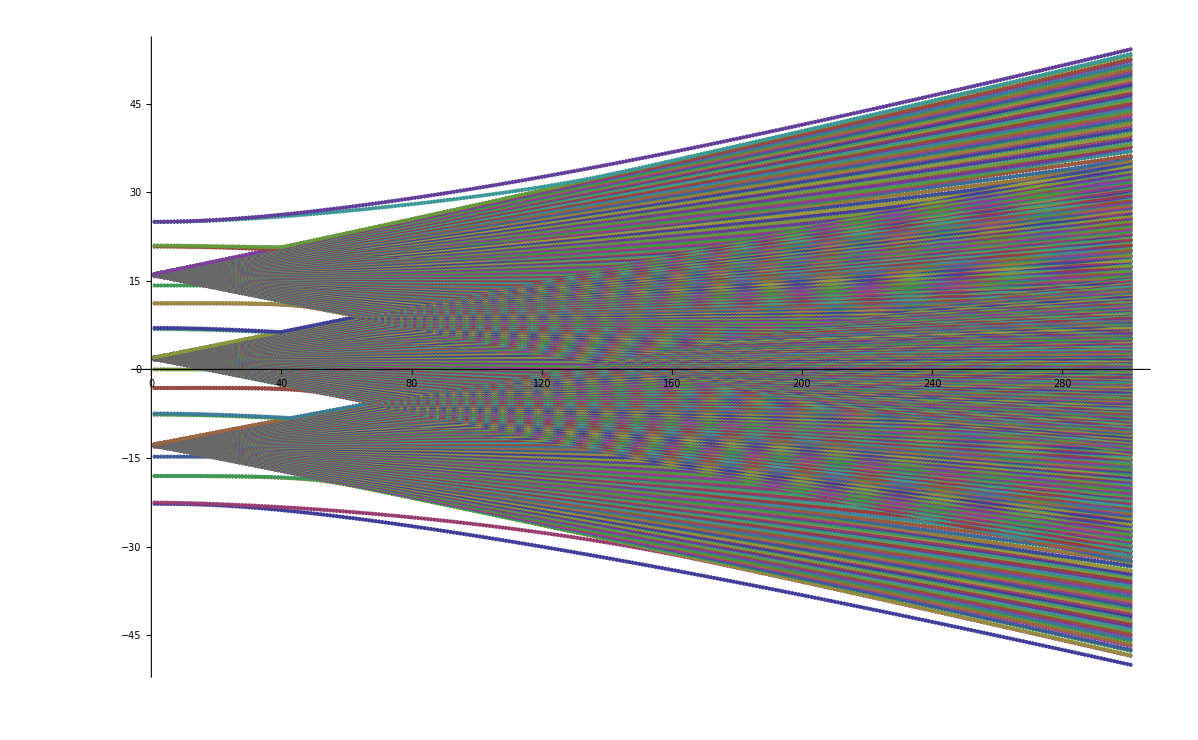

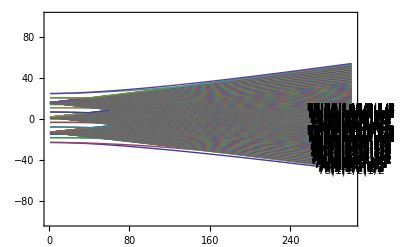

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

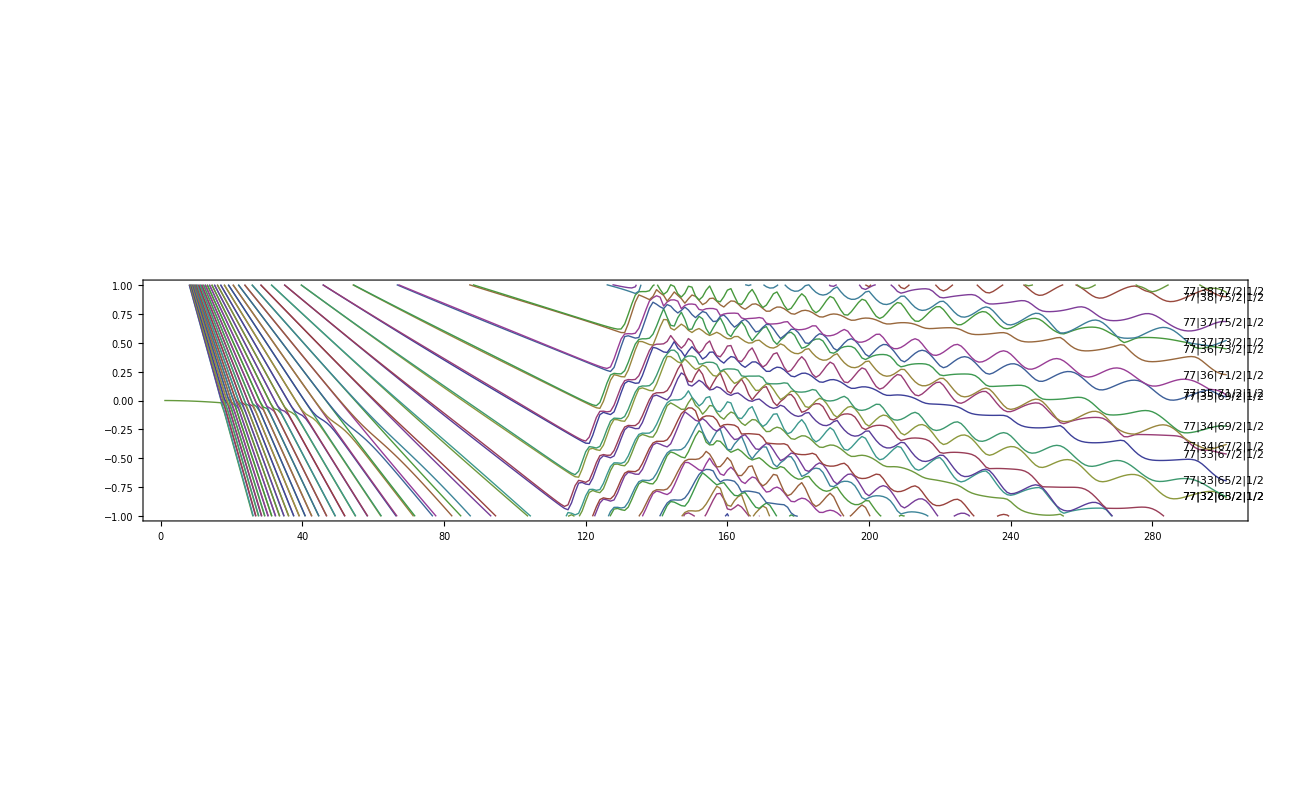

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX= 50;
ELabel=49;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=0.1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

{{49,-24.3328,78|1|1/2|1/2},{49,-23.6215,78|1|3/2|1/2},{49,-18.6638,77|2|3/2|1/2},{49,-18.5778,77|2|5/2|1/2},{49,-18.1839,79|0|1/2|1/2},{49,-18.1649,76|3|7/2|1/2},{49,-18.0247,76|3|5/2|1/2},{49,-18.0104,76|4|7/2|1/2},{49,-17.8713,76|4|9/2|1/2},{49,-17.8594,76|5|9/2|1/2},{49,-17.7204,76|5|11/2|1/2},{49,-17.7101,76|6|11/2|1/2},{49,-17.5711,76|6|13/2|1/2},{49,-17.5619,76|7|13/2|1/2},{49,-17.4226,76|7|15/2|1/2},{49,-17.4144,76|8|15/2|1/2},{49,-17.2748,76|8|17/2|1/2},{49,-17.2673,76|9|17/2|1/2},{49,-17.1275,76|9|19/2|1/2},{49,-17.1206,76|10|19/2|1/2},{49,-16.9805,76|10|21/2|1/2},{49,-16.9742,76|11|21/2|1/2},{49,-16.8339,76|11|23/2|1/2},{49,-16.828,76|12|23/2|1/2},{49,-16.6874,76|12|25/2|1/2},{49,-16.682,76|13|25/2|1/2},{49,-16.5412,76|13|27/2|1/2},{49,-16.5362,76|14|27/2|1/2},{49,-16.3952,76|14|29/2|1/2},{49,-16.3904,76|15|29/2|1/2},{49,-16.2492,76|15|31/2|1/2},{49,-16.2448,76|16|31/2|1/2},{49,-16.1035,76|16|33/2|1/2},{49,-16.0993,76|17|33/2|1/2},{49,-15.9578,76|17|35/2|1/2},{49,-15.9538,76|18|35/2|1/2},{49,-15.8122,76|18|37/2|1/2},{49,-15.8085,76|19|37/2|1/2},{49,-15.6668,76|19|39/2|1/2},{49,-15.6632,76|20|39/2|1/2},{49,-15.5216,76|20|41/2|1/2},{49,-15.5179,76|21|41/2|1/2},{49,-15.3765,76|21|43/2|1/2},{49,-15.3727,76|22|43/2|1/2},{49,-15.2322,76|22|45/2|1/2},{49,-15.2275,76|23|45/2|1/2},{49,-15.0911,76|23|47/2|1/2},{49,-15.0824,76|24|47/2|1/2},{49,-15.003,76|24|49/2|1/2},{49,-14.9373,76|25|49/2|1/2},{49,-14.9296,76|25|51/2|1/2},{49,-14.7922,76|26|51/2|1/2},{49,-14.7902,76|26|53/2|1/2},{49,-14.6471,76|27|53/2|1/2},{49,-14.6461,76|27|55/2|1/2},{49,-14.502,76|28|55/2|1/2},{49,-14.5013,76|28|57/2|1/2},{49,-14.3569,76|29|57/2|1/2},{49,-14.3563,76|29|59/2|1/2},{49,-14.2118,76|30|59/2|1/2},{49,-14.2112,76|30|61/2|1/2},{49,-14.0667,76|31|61/2|1/2},{49,-14.066,76|31|63/2|1/2},{49,-13.9216,76|32|63/2|1/2},{49,-13.9208,76|32|65/2|1/2},{49,-13.7764,76|33|65/2|1/2},{49,-13.7756,76|33|67/2|1/2},{49,-13.6313,76|34|67/2|1/2},{49,-13.6303,76|34|69/2|1/2},{49,-13.4861,76|35|69/2|1/2},{49,-13.485,76|35|71/2|1/2},{49,-13.3408,76|36|71/2|1/2},{49,-13.3396,76|36|73/2|1/2},{49,-13.1956,76|37|73/2|1/2},{49,-13.1941,76|37|75/2|1/2},{49,-13.0502,76|38|75/2|1/2},{49,-13.0487,76|38|77/2|1/2},{49,-12.9049,76|39|77/2|1/2},{49,-12.9031,76|39|79/2|1/2},{49,-12.7595,76|40|79/2|1/2},{49,-12.7576,76|40|81/2|1/2},{49,-12.6141,76|41|81/2|1/2},{49,-12.612,76|41|83/2|1/2},{49,-12.4687,76|42|83/2|1/2},{49,-12.4664,76|42|85/2|1/2},{49,-12.3233,76|43|85/2|1/2},{49,-12.3208,76|43|87/2|1/2},{49,-12.1778,76|44|87/2|1/2},{49,-12.1751,76|44|89/2|1/2},{49,-12.0323,76|45|89/2|1/2},{49,-12.0295,76|45|91/2|1/2},{49,-11.8868,76|46|91/2|1/2},{49,-11.8837,76|46|93/2|1/2},{49,-11.7412,76|47|93/2|1/2},{49,-11.738,76|47|95/2|1/2},{49,-11.5956,76|48|95/2|1/2},{49,-11.5922,76|48|97/2|1/2},{49,-11.45,76|49|97/2|1/2},{49,-11.4463,76|49|99/2|1/2},{49,-11.3043,76|50|99/2|1/2},{49,-11.3004,76|50|101/2|1/2},{49,-11.1585,76|51|101/2|1/2},{49,-11.1544,76|51|103/2|1/2},{49,-11.0127,76|52|103/2|1/2},{49,-11.0083,76|52|105/2|1/2},{49,-10.8668,76|53|105/2|1/2},{49,-10.8622,76|53|107/2|1/2},{49,-10.7208,76|54|107/2|1/2},{49,-10.716,76|54|109/2|1/2},{49,-10.5748,76|55|109/2|1/2},{49,-10.5697,76|55|111/2|1/2},{49,-10.4288,76|56|111/2|1/2},{49,-10.4233,76|56|113/2|1/2},{49,-10.2826,76|57|113/2|1/2},{49,-10.2769,76|57|115/2|1/2},{49,-10.1364,76|58|115/2|1/2},{49,-10.1304,76|58|117/2|1/2},{49,-9.99007,76|59|117/2|1/2},{49,-9.98377,76|59|119/2|1/2},{49,-9.8437,76|60|119/2|1/2},{49,-9.83707,76|60|121/2|1/2},{49,-9.69726,76|61|121/2|1/2},{49,-9.69027,76|61|123/2|1/2},{49,-9.55074,76|62|123/2|1/2},{49,-9.54337,76|62|125/2|1/2},{49,-9.40414,76|63|125/2|1/2},{49,-9.39638,76|63|127/2|1/2},{49,-9.25749,76|64|127/2|1/2},{49,-9.24929,76|64|129/2|1/2},{49,-9.11078,76|65|129/2|1/2},{49,-9.10213,76|65|131/2|1/2},{49,-8.96408,76|66|131/2|1/2},{49,-8.95496,76|66|133/2|1/2},{49,-8.81751,76|67|133/2|1/2},{49,-8.80795,76|67|135/2|1/2},{49,-8.67175,76|68|135/2|1/2},{49,-8.66196,76|68|137/2|1/2},{49,-8.54133,76|69|137/2|1/2},{49,-8.5229,76|69|139/2|1/2},{49,-8.48891,76|70|139/2|1/2},{49,-8.42339,76|70|141/2|1/2},{49,-8.36554,76|71|141/2|1/2},{49,-8.35082,76|71|143/2|1/2},{49,-8.22226,76|72|143/2|1/2},{49,-8.20783,76|72|145/2|1/2},{49,-8.07514,76|73|145/2|1/2},{49,-8.05931,76|73|147/2|1/2},{49,-7.92693,76|74|147/2|1/2},{49,-7.90906,76|74|149/2|1/2},{49,-7.77784,76|75|149/2|1/2},{49,-7.75685,76|75|151/2|1/2},{49,-7.62758,79|1|1/2|1/2},{49,-7.60071,79|1|3/2|1/2},{49,-3.70611,78|2|3/2|1/2},{49,-3.66267,78|2|5/2|1/2},{49,-3.51423,80|0|1/2|1/2},{49,-3.50111,77|3|7/2|1/2},{49,-3.35861,77|3|5/2|1/2},{49,-3.34925,77|4|7/2|1/2},{49,-3.20675,77|4|9/2|1/2},{49,-3.19908,77|5|9/2|1/2},{49,-3.05641,77|5|11/2|1/2},{49,-3.04973,77|6|11/2|1/2},{49,-2.90688,77|6|13/2|1/2},{49,-2.90088,77|7|13/2|1/2},{49,-2.75786,77|7|15/2|1/2},{49,-2.75236,77|8|15/2|1/2},{49,-2.60918,77|8|17/2|1/2},{49,-2.60408,77|9|17/2|1/2},{49,-2.46074,77|9|19/2|1/2},{49,-2.45597,77|10|19/2|1/2},{49,-2.31249,77|10|21/2|1/2},{49,-2.308,77|11|21/2|1/2},{49,-2.16439,77|11|23/2|1/2},{49,-2.16014,77|12|23/2|1/2},{49,-2.0164,77|12|25/2|1/2},{49,-2.01237,77|13|25/2|1/2},{49,-1.86851,77|13|27/2|1/2},{49,-1.86468,77|14|27/2|1/2},{49,-1.7207,77|14|29/2|1/2},{49,-1.71704,77|15|29/2|1/2},{49,-1.57297,77|15|31/2|1/2},{49,-1.56946,77|16|31/2|1/2},{49,-1.42531,77|16|33/2|1/2},{49,-1.42192,77|17|33/2|1/2},{49,-1.27772,77|17|35/2|1/2},{49,-1.27442,77|18|35/2|1/2},{49,-1.13021,77|18|37/2|1/2},{49,-1.12695,77|19|37/2|1/2},{49,-0.982785,77|19|39/2|1/2},{49,-0.979509,77|20|39/2|1/2},{49,-0.835497,77|20|41/2|1/2},{49,-0.832089,77|21|41/2|1/2},{49,-0.688431,77|21|43/2|1/2},{49,-0.684688,77|22|43/2|1/2},{49,-0.54184,77|22|45/2|1/2},{49,-0.537301,77|23|45/2|1/2},{49,-0.396702,77|23|47/2|1/2},{49,-0.389925,77|24|47/2|1/2},{49,-0.261034,77|24|49/2|1/2},{49,-0.242556,77|25|49/2|1/2},{49,-0.188551,77|25|51/2|1/2},{49,-0.0951887,77|26|51/2|1/2},{49,-0.0857398,77|26|53/2|1/2},{49,0.0521801,77|27|53/2|1/2},{49,0.0563079,77|27|55/2|1/2},{49,0.199554,77|28|55/2|1/2},{49,0.202239,77|28|57/2|1/2},{49,0.346936,77|29|57/2|1/2},{49,0.349033,77|29|59/2|1/2},{49,0.494327,77|30|59/2|1/2},{49,0.496154,77|30|61/2|1/2},{49,0.641728,77|31|61/2|1/2},{49,0.643437,77|31|63/2|1/2},{49,0.789142,77|32|63/2|1/2},{49,0.790817,77|32|65/2|1/2},{49,0.936571,77|33|65/2|1/2},{49,0.938266,77|33|67/2|1/2},{49,1.08402,77|34|67/2|1/2},{49,1.08577,77|34|69/2|1/2},{49,1.23149,77|35|69/2|1/2},{49,1.23333,77|35|71/2|1/2},{49,1.379,77|36|71/2|1/2},{49,1.38094,77|36|73/2|1/2},{49,1.52654,77|37|73/2|1/2},{49,1.52859,77|37|75/2|1/2},{49,1.67412,77|38|75/2|1/2},{49,1.6763,77|38|77/2|1/2},{49,1.82173,77|39|77/2|1/2},{49,1.82404,77|39|79/2|1/2},{49,1.96935,77|40|79/2|1/2},{49,1.97181,77|40|81/2|1/2},{49,2.11698,77|41|81/2|1/2},{49,2.1196,77|41|83/2|1/2},{49,2.26461,77|42|83/2|1/2},{49,2.26739,77|42|85/2|1/2},{49,2.41224,77|43|85/2|1/2},{49,2.41518,77|43|87/2|1/2},{49,2.55986,77|44|87/2|1/2},{49,2.56298,77|44|89/2|1/2},{49,2.70748,77|45|89/2|1/2},{49,2.71077,77|45|91/2|1/2},{49,2.8551,77|46|91/2|1/2},{49,2.85858,77|46|93/2|1/2},{49,3.00274,77|47|93/2|1/2},{49,3.0064,77|47|95/2|1/2},{49,3.15038,77|48|95/2|1/2},{49,3.15424,77|48|97/2|1/2},{49,3.29805,77|49|97/2|1/2},{49,3.30211,77|49|99/2|1/2},{49,3.44573,77|50|99/2|1/2},{49,3.45001,77|50|101/2|1/2},{49,3.59344,77|51|101/2|1/2},{49,3.59793,77|51|103/2|1/2},{49,3.74117,77|52|103/2|1/2},{49,3.74588,77|52|105/2|1/2},{49,3.88893,77|53|105/2|1/2},{49,3.89387,77|53|107/2|1/2},{49,4.03672,77|54|107/2|1/2},{49,4.0419,77|54|109/2|1/2},{49,4.18453,77|55|109/2|1/2},{49,4.18997,77|55|111/2|1/2},{49,4.33238,77|56|111/2|1/2},{49,4.33808,77|56|113/2|1/2},{49,4.48025,77|57|113/2|1/2},{49,4.48623,77|57|115/2|1/2},{49,4.62817,77|58|115/2|1/2},{49,4.63443,77|58|117/2|1/2},{49,4.77611,77|59|117/2|1/2},{49,4.78268,77|59|119/2|1/2},{49,4.92409,77|60|119/2|1/2},{49,4.93097,77|60|121/2|1/2},{49,5.07209,77|61|121/2|1/2},{49,5.07931,77|61|123/2|1/2},{49,5.22011,77|62|123/2|1/2},{49,5.22769,77|62|125/2|1/2},{49,5.3681,77|63|125/2|1/2},{49,5.37606,77|63|127/2|1/2},{49,5.516,77|64|127/2|1/2},{49,5.52436,77|64|129/2|1/2},{49,5.66354,77|65|129/2|1/2},{49,5.67229,77|65|131/2|1/2},{49,5.80925,77|66|131/2|1/2},{49,5.81849,77|66|133/2|1/2},{49,5.91725,77|67|133/2|1/2},{49,5.9538,77|67|135/2|1/2},{49,5.98177,77|68|135/2|1/2},{49,6.02143,77|68|137/2|1/2},{49,6.11736,77|69|137/2|1/2},{49,6.12897,77|69|139/2|1/2},{49,6.26358,77|70|139/2|1/2},{49,6.27532,77|70|141/2|1/2},{49,6.41172,77|71|141/2|1/2},{49,6.42423,77|71|143/2|1/2},{49,6.56052,77|72|143/2|1/2},{49,6.57401,77|72|145/2|1/2},{49,6.70976,77|73|145/2|1/2},{49,6.72447,77|73|147/2|1/2},{49,6.85941,77|74|147/2|1/2},{49,6.8757,77|74|149/2|1/2},{49,7.00957,77|75|149/2|1/2},{49,7.028,77|75|151/2|1/2},{49,7.1604,77|76|151/2|1/2},{49,7.18206,77|76|153/2|1/2},{49,7.3123,80|1|1/2|1/2},{49,7.33995,80|1|3/2|1/2},{49,10.4751,79|2|3/2|1/2},{49,10.5202,79|2|5/2|1/2},{49,10.6308,81|0|1/2|1/2},{49,10.6482,78|3|7/2|1/2},{49,10.7828,78|3|5/2|1/2},{49,10.7931,78|4|7/2|1/2},{49,10.9339,78|4|9/2|1/2},{49,10.9415,78|5|9/2|1/2},{49,11.0846,78|5|11/2|1/2},{49,11.0909,78|6|11/2|1/2},{49,11.2351,78|6|13/2|1/2},{49,11.2405,78|7|13/2|1/2},{49,11.3854,78|7|15/2|1/2},{49,11.3902,78|8|15/2|1/2},{49,11.5355,78|8|17/2|1/2},{49,11.54,78|9|17/2|1/2},{49,11.6856,78|9|19/2|1/2},{49,11.6897,78|10|19/2|1/2},{49,11.8356,78|10|21/2|1/2},{49,11.8395,78|11|21/2|1/2},{49,11.9855,78|11|23/2|1/2},{49,11.9892,78|12|23/2|1/2},{49,12.1354,78|12|25/2|1/2},{49,12.1389,78|13|25/2|1/2},{49,12.2852,78|13|27/2|1/2},{49,12.2885,78|14|27/2|1/2},{49,12.4349,78|14|29/2|1/2},{49,12.4381,78|15|29/2|1/2},{49,12.5846,78|15|31/2|1/2},{49,12.5877,78|16|31/2|1/2},{49,12.7342,78|16|33/2|1/2},{49,12.7372,78|17|33/2|1/2},{49,12.8837,78|17|35/2|1/2},{49,12.8867,78|18|35/2|1/2},{49,13.0332,78|18|37/2|1/2},{49,13.0361,78|19|37/2|1/2},{49,13.1825,78|19|39/2|1/2},{49,13.1855,78|20|39/2|1/2},{49,13.3317,78|20|41/2|1/2},{49,13.3349,78|21|41/2|1/2},{49,13.4806,78|21|43/2|1/2},{49,13.4842,78|22|43/2|1/2},{49,13.6291,78|22|45/2|1/2},{49,13.6335,78|23|45/2|1/2},{49,13.7767,78|23|47/2|1/2},{49,13.7827,78|24|47/2|1/2},{49,13.9205,78|24|49/2|1/2},{49,13.9319,78|25|49/2|1/2},{49,14.0363,78|25|51/2|1/2},{49,14.0811,78|26|51/2|1/2},{49,14.1096,78|26|53/2|1/2},{49,14.2302,78|27|53/2|1/2},{49,14.2391,78|27|55/2|1/2},{49,14.3793,78|28|55/2|1/2},{49,14.3844,78|28|57/2|1/2},{49,14.5283,78|29|57/2|1/2},{49,14.5321,78|29|59/2|1/2},{49,14.6773,78|30|59/2|1/2},{49,14.6805,78|30|61/2|1/2},{49,14.8263,78|31|61/2|1/2},{49,14.8292,78|31|63/2|1/2},{49,14.9753,78|32|63/2|1/2},{49,14.978,78|32|65/2|1/2},{49,15.1243,78|33|65/2|1/2},{49,15.1269,78|33|67/2|1/2},{49,15.2732,78|34|67/2|1/2},{49,15.2758,78|34|69/2|1/2},{49,15.4221,78|35|69/2|1/2},{49,15.4247,78|35|71/2|1/2},{49,15.5711,78|36|71/2|1/2},{49,15.5737,78|36|73/2|1/2},{49,15.72,78|37|73/2|1/2},{49,15.7227,78|37|75/2|1/2},{49,15.8689,78|38|75/2|1/2},{49,15.8717,78|38|77/2|1/2},{49,16.0178,78|39|77/2|1/2},{49,16.0208,78|39|79/2|1/2},{49,16.1668,78|40|79/2|1/2},{49,16.1698,78|40|81/2|1/2},{49,16.3157,78|41|81/2|1/2},{49,16.3189,78|41|83/2|1/2},{49,16.4646,78|42|83/2|1/2},{49,16.4679,78|42|85/2|1/2},{49,16.6135,78|43|85/2|1/2},{49,16.6169,78|43|87/2|1/2},{49,16.7624,78|44|87/2|1/2},{49,16.7659,78|44|89/2|1/2},{49,16.9112,78|45|89/2|1/2},{49,16.9149,78|45|91/2|1/2},{49,17.06,78|46|91/2|1/2},{49,17.0639,78|46|93/2|1/2},{49,17.2088,78|47|93/2|1/2},{49,17.2129,78|47|95/2|1/2},{49,17.3576,78|48|95/2|1/2},{49,17.3619,78|48|97/2|1/2},{49,17.5064,78|49|97/2|1/2},{49,17.5109,78|49|99/2|1/2},{49,17.6552,78|50|99/2|1/2},{49,17.6599,78|50|101/2|1/2},{49,17.8041,78|51|101/2|1/2},{49,17.8089,78|51|103/2|1/2},{49,17.9529,78|52|103/2|1/2},{49,17.958,78|52|105/2|1/2},{49,18.1018,78|53|105/2|1/2},{49,18.107,78|53|107/2|1/2},{49,18.2506,78|54|107/2|1/2},{49,18.2562,78|54|109/2|1/2},{49,18.3995,78|55|109/2|1/2},{49,18.4053,78|55|111/2|1/2},{49,18.5485,78|56|111/2|1/2},{49,18.5545,78|56|113/2|1/2},{49,18.6974,78|57|113/2|1/2},{49,18.7037,78|57|115/2|1/2},{49,18.8464,78|58|115/2|1/2},{49,18.853,78|58|117/2|1/2},{49,18.9954,78|59|117/2|1/2},{49,19.0023,78|59|119/2|1/2},{49,19.1444,78|60|119/2|1/2},{49,19.1517,78|60|121/2|1/2},{49,19.2934,78|61|121/2|1/2},{49,19.3012,78|61|123/2|1/2},{49,19.4424,78|62|123/2|1/2},{49,19.4507,78|62|125/2|1/2},{49,19.5912,78|63|125/2|1/2},{49,19.6002,78|63|127/2|1/2},{49,19.7394,78|64|127/2|1/2},{49,19.7499,78|64|129/2|1/2},{49,19.8845,78|65|129/2|1/2},{49,19.8995,78|65|131/2|1/2},{49,19.9853,78|66|131/2|1/2},{49,20.0492,78|66|133/2|1/2},{49,20.055,78|67|133/2|1/2},{49,20.1957,78|67|135/2|1/2},{49,20.1988,78|68|135/2|1/2},{49,20.3438,78|68|137/2|1/2},{49,20.3478,78|69|137/2|1/2},{49,20.4929,78|69|139/2|1/2},{49,20.4948,78|70|139/2|1/2},{49,20.6226,78|70|141/2|1/2},{49,20.643,78|71|141/2|1/2},{49,20.6899,78|71|143/2|1/2},{49,20.793,78|72|143/2|1/2},{49,20.8134,78|72|145/2|1/2},{49,20.9434,78|73|145/2|1/2},{49,20.9607,78|73|147/2|1/2},{49,21.0941,78|74|147/2|1/2},{49,21.1113,78|74|149/2|1/2},{49,21.2451,78|75|149/2|1/2},{49,21.2633,78|75|151/2|1/2},{49,21.3967,78|76|151/2|1/2},{49,21.4166,78|76|153/2|1/2},{49,21.5489,78|77|153/2|1/2},{49,21.5718,78|77|155/2|1/2},{49,21.7022,81|1|1/2|1/2},{49,21.7309,81|1|3/2|1/2},{49,26.2793,80|2|3/2|1/2},{49,26.7232,80|2|5/2|1/2}}

-Graphics-

-Graphics-

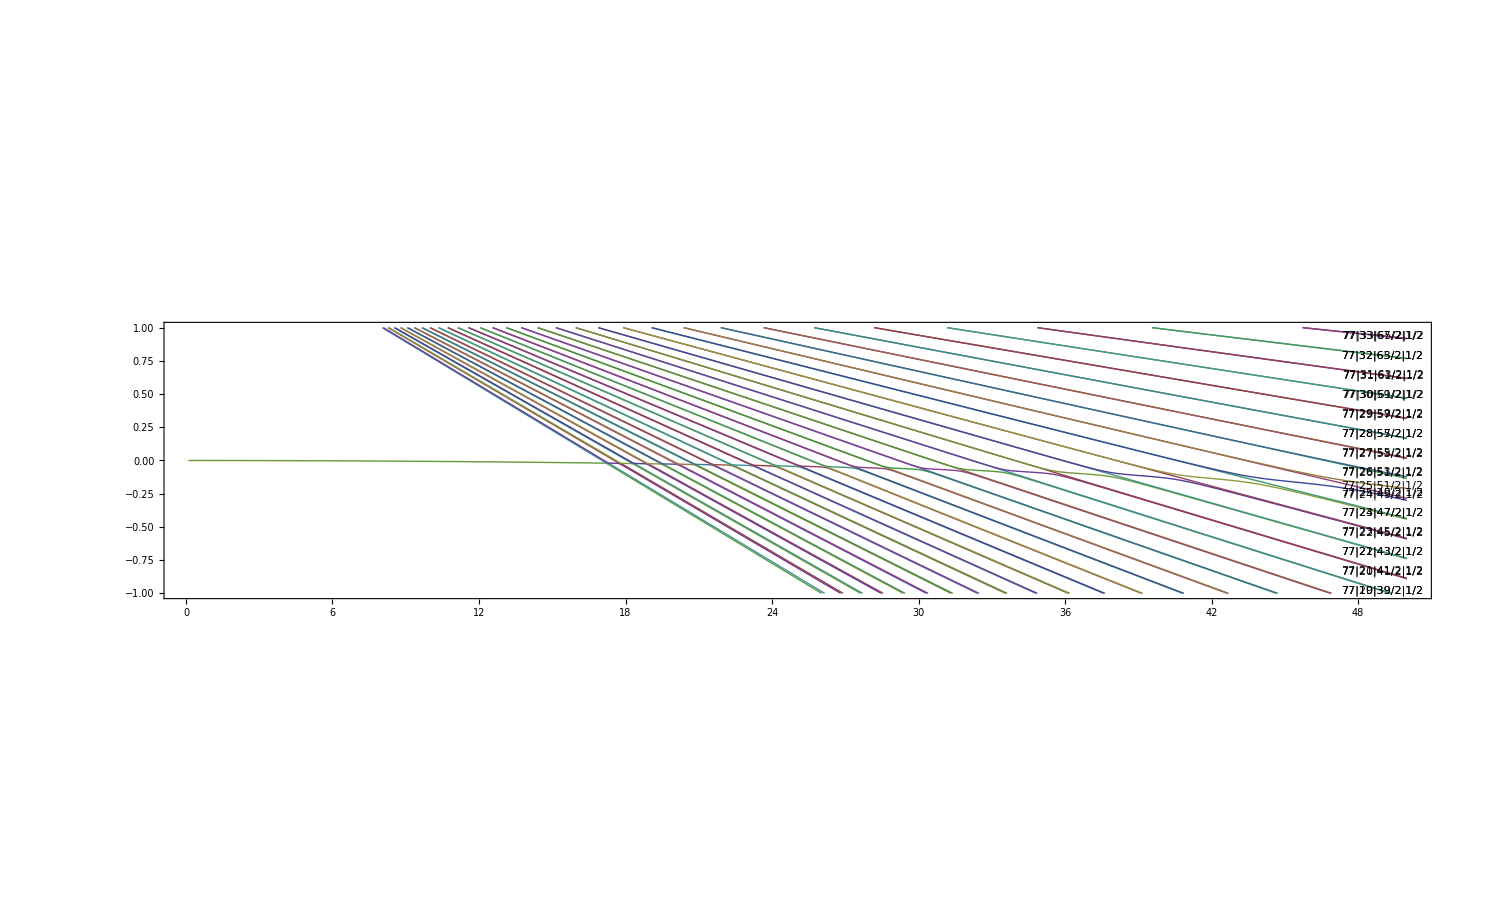

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
(*LabelList[[116]]

MPList[[116]]

(*MPListExport: Generate list to be read by Origin *)

Efieldlist = {};

E0=EMIN;


While[E0<EMAX,E0=E0+EStep;Efieldlist=Join[Efieldlist,{E0}]] ;
E0=EMIN;

Efieldlist


Clear[i,k,L,MPListExport,R]
NE0=(EMAX-EMIN)/EStep;
MPListExport=Array[0,{Length[NList],NE0}];
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)



Clear[i];
j=0;
While[j<NE0,
j++;
For[i=1,i≤Length[NList],i++,
MPListExport[[i,j]]=MPList[[i,j,2]] 
 ]
] ;

MPListExport



Export["Stark_Shifts_around_60s.dat",MPListExport]
Export["Electric_fields_for_Stark_Shifts_around_60s.dat",Efieldlist]

Export["60s_stark_Shift.dat",MPList[[116]]] *)
```

60|0|1/2|1/2

{{1,-8.9749×10^-6},{2,-0.0000358999},{3,-0.0000807756},{4,-0.000143603},{5,-0.000224385},{6,-0.000323122},{7,-0.000439819},{8,-0.000574477},{9,-0.000727101},{10,-0.000897695},{11,-0.00108626},{12,-0.00129281},{13,-0.00151735},{14,-0.00175988},{15,-0.0020204},{16,-0.00229894},{17,-0.00259549},{18,-0.00291006},{19,-0.00324267},{20,-0.00359332},{21,-0.00396203},{22,-0.0043488},{23,-0.00475365},{24,-0.0051766},{25,-0.00561765},{26,-0.00607681},{27,-0.00655412},{28,-0.00704957},{29,-0.00756319},{30,-0.008095},{31,-0.00864501},{32,-0.00921324},{33,-0.00979973},{34,-0.0104045},{35,-0.0110275},{36,-0.0116689},{37,-0.0123286},{38,-0.0130066},{39,-0.0137031},{40,-0.014418},{41,-0.0151513},{42,-0.0159031},{43,-0.0166735},{44,-0.0174624},{45,-0.0182699},{46,-0.019096},{47,-0.0199409},{48,-0.0208044},{49,-0.0216867},{50,-0.0225878},{51,-0.0235078},{52,-0.0244468},{53,-0.0254047},{54,-0.0263816},{55,-0.0273777},{56,-0.0283929},{57,-0.0294274},{58,-0.0304812},{59,-0.0315545},{60,-0.0326473},{61,-0.0337596},{62,-0.0348917},{63,-0.0360437},{64,-0.0372156},{65,-0.0384077},{66,-0.0396201},{67,-0.0408529},{68,-0.0421065},{69,-0.0433812},{70,-0.0446771},{71,-0.045995},{72,-0.0473352},{73,-0.0486988},{74,-0.0500873},{75,-0.0515034},{76,-0.0529536},{77,-0.0544608},{78,-0.0562774},{79,-0.0954785},{80,-0.155665},{81,-0.215968},{82,-0.276291},{83,-0.336621},{84,-0.396955},{85,-0.45729},{86,-0.517626},{87,-0.577963},{88,-0.6383},{89,-0.698637},{90,-0.758974},{91,-0.81931},{92,-0.879646},{93,-0.939982},{94,-1.00032},{95,-1.06065},{96,-1.12098},{97,-1.18132},{98,-1.24165},{99,-1.30198},{100,-1.36231},{101,-1.42264},{102,-1.48296},{103,-1.54329},{104,-1.60362},{105,-1.66394},{106,-1.72426},{107,-1.78458},{108,-1.8449},{109,-1.90522},{110,-1.96553},{111,-2.02584},{112,-2.08616},{113,-2.14646},{114,-2.20677},{115,-2.26707},{116,-2.32738},{117,-2.38768},{118,-2.44797},{119,-2.50827},{120,-2.56856},{121,-2.62885},{122,-2.68913},{123,-2.74941},{124,-2.80969},{125,-2.86996},{126,-2.93023},{127,-2.9905},{128,-3.05076},{129,-3.11102},{130,-3.17128},{131,-3.23153},{132,-3.29177},{133,-3.35201},{134,-3.41225},{135,-3.47248},{136,-3.5327},{137,-3.59292},{138,-3.65313},{139,-3.71334},{140,-3.77354},{141,-3.83373},{142,-3.89392},{143,-3.9541},{144,-4.01427},{145,-4.07443},{146,-4.13459},{147,-4.19473},{148,-4.25487},{149,-4.315},{150,-4.37512},{151,-4.43523},{152,-4.49533},{153,-4.55541},{154,-4.61549},{155,-4.67555},{156,-4.73561},{157,-4.79564},{158,-4.85567},{159,-4.91568},{160,-4.97568},{161,-5.03566},{162,-5.09562},{163,-5.15557},{164,-5.2155},{165,-5.27542},{166,-5.33531},{167,-5.39518},{168,-5.45504},{169,-5.51487},{170,-5.57468},{171,-5.63446},{172,-5.69422},{173,-5.75395},{174,-5.81366},{175,-5.87333},{176,-5.93298},{177,-5.99259},{178,-6.05217},{179,-6.11171},{180,-6.17122},{181,-6.23069},{182,-6.29012},{183,-6.3495},{184,-6.40884},{185,-6.46812},{186,-6.52736},{187,-6.58655},{188,-6.64567},{189,-6.70474},{190,-6.76375},{191,-6.82268},{192,-6.88155},{193,-6.94034},{194,-6.99906},{195,-7.05769},{196,-7.11623},{197,-7.17468},{198,-7.23303},{199,-7.29127},{200,-7.3494},{201,-7.40742},{202,-7.46531},{203,-7.52307},{204,-7.5807},{205,-7.63817},{206,-7.6955},{207,-7.75266},{208,-7.80965},{209,-7.86646},{210,-7.92309},{211,-7.97952},{212,-8.03576},{213,-8.09178},{214,-8.14758},{215,-8.20317},{216,-8.25852},{217,-8.31365},{218,-8.36854},{219,-8.42319},{220,-8.4776},{221,-8.53177},{222,-8.58571},{223,-8.63941},{224,-8.69288},{225,-8.74614},{226,-8.79918},{227,-8.85203},{228,-8.90469},{229,-8.95719},{230,-9.00955},{231,-9.0618},{232,-9.11394},{233,-9.16602},{234,-9.21806},{235,-9.27009},{236,-9.32212},{237,-9.37418},{238,-9.42631},{239,-9.4785},{240,-9.53079},{241,-9.58319},{242,-9.6357},{243,-9.68835},{244,-9.74113},{245,-9.79407},{246,-9.84715},{247,-9.90039},{248,-9.95378},{249,-10.0073},{250,-10.061},{251,-10.1149},{252,-10.1689},{253,-10.2231},{254,-10.2774},{255,-10.3318},{256,-10.3864},{257,-10.4412},{258,-10.496},{259,-10.551},{260,-10.6061},{261,-10.6614},{262,-10.7167},{263,-10.7721},{264,-10.8277},{265,-10.8833},{266,-10.9391},{267,-10.9949},{268,-11.0509},{269,-11.1069},{270,-11.163},{271,-11.2191},{272,-11.2754},{273,-11.3317},{274,-11.3881},{275,-11.4445},{276,-11.501},{277,-11.5576},{278,-11.6142},{279,-11.6709},{280,-11.7277},{281,-11.7845},{282,-11.8413},{283,-11.8982},{284,-11.9551},{285,-12.012},{286,-12.0691},{287,-12.1261},{288,-12.1832},{289,-12.2403},{290,-12.2974},{291,-12.3546},{292,-12.4118},{293,-12.4691},{294,-12.5263},{295,-12.5836},{296,-12.6409},{297,-12.6983},{298,-12.7556},{299,-12.813},{300,-12.8704},{301,-12.9278}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301}

{«1»}

Stark_Shifts_around_60s.dat

Electric_fields_for_Stark_Shifts_around_60s.dat

60s_stark_Shift.dat

```mathematica
LabelList[[112]]
LabelList[[113]]

MPList[[112]]

Export["59p1_2_stark_Shift.dat",MPList[[112]]] 
Export["59p3_2_stark_Shift.dat",MPList[[113]]]
```

59|1|1/2|1/2

59|1|3/2|1/2

{{1,-18.999},{2,-18.9992},{3,-18.9994},{4,-18.9998},{5,-19.0002},{6,-19.0008},{7,-19.0014},{8,-19.0022},{9,-19.003},{10,-19.004},{11,-19.005},{12,-19.0062},{13,-19.0074},{14,-19.0088},{15,-19.0102},{16,-19.0117},{17,-19.0134},{18,-19.0151},{19,-19.017},{20,-19.0189},{21,-19.021},{22,-19.0231},{23,-19.0253},{24,-19.0277},{25,-19.0301},{26,-19.0326},{27,-19.0353},{28,-19.038},{29,-19.0408},{30,-19.0438},{31,-19.0468},{32,-19.0499},{33,-19.0532},{34,-19.0565},{35,-19.0599},{36,-19.0634},{37,-19.067},{38,-19.0707},{39,-19.0746},{40,-19.0785},{41,-19.0825},{42,-19.0866},{43,-19.0908},{44,-19.0951},{45,-19.0995},{46,-19.104},{47,-19.1086},{48,-19.1133},{49,-19.118},{50,-19.1229},{51,-19.1279},{52,-19.133},{53,-19.1381},{54,-19.1434},{55,-19.1488},{56,-19.1542},{57,-19.1598},{58,-19.1654},{59,-19.1712},{60,-19.177},{61,-19.1829},{62,-19.189},{63,-19.1951},{64,-19.2013},{65,-19.2076},{66,-19.214},{67,-19.2205},{68,-19.2271},{69,-19.2338},{70,-19.2405},{71,-19.2474},{72,-19.2544},{73,-19.2614},{74,-19.2685},{75,-19.2758},{76,-19.2831},{77,-19.2905},{78,-19.298},{79,-19.3056},{80,-19.3133},{81,-19.3211},{82,-19.329},{83,-19.3369},{84,-19.345},{85,-19.3531},{86,-19.3613},{87,-19.3697},{88,-19.3781},{89,-19.3866},{90,-19.3951},{91,-19.4038},{92,-19.4126},{93,-19.4214},{94,-19.4303},{95,-19.4394},{96,-19.4485},{97,-19.4577},{98,-19.4669},{99,-19.4763},{100,-19.4857},{101,-19.4953},{102,-19.5049},{103,-19.5146},{104,-19.5243},{105,-19.5342},{106,-19.5441},{107,-19.5542},{108,-19.5643},{109,-19.5745},{110,-19.5847},{111,-19.5951},{112,-19.6055},{113,-19.616},{114,-19.6266},{115,-19.6373},{116,-19.648},{117,-19.6589},{118,-19.6698},{119,-19.6807},{120,-19.6918},{121,-19.7029},{122,-19.7141},{123,-19.7254},{124,-19.7368},{125,-19.7482},{126,-19.7597},{127,-19.7713},{128,-19.783},{129,-19.7947},{130,-19.8065},{131,-19.8184},{132,-19.8303},{133,-19.8423},{134,-19.8544},{135,-19.8665},{136,-19.8788},{137,-19.891},{138,-19.9034},{139,-19.9158},{140,-19.9283},{141,-19.9409},{142,-19.9535},{143,-19.9662},{144,-19.9789},{145,-19.9917},{146,-20.0046},{147,-20.0175},{148,-20.0305},{149,-20.0436},{150,-20.0567},{151,-20.0698},{152,-20.0831},{153,-20.0964},{154,-20.1097},{155,-20.1231},{156,-20.1366},{157,-20.1501},{158,-20.1636},{159,-20.1772},{160,-20.1909},{161,-20.2046},{162,-20.2184},{163,-20.2322},{164,-20.2461},{165,-20.26},{166,-20.2739},{167,-20.2879},{168,-20.3019},{169,-20.316},{170,-20.3301},{171,-20.3443},{172,-20.3585},{173,-20.3727},{174,-20.387},{175,-20.4012},{176,-20.4155},{177,-20.4299},{178,-20.4442},{179,-20.4586},{180,-20.473},{181,-20.4874},{182,-20.5017},{183,-20.5161},{184,-20.5304},{185,-20.5448},{186,-20.559},{187,-20.5732},{188,-20.5872},{189,-20.601},{190,-20.6146},{191,-20.6275},{192,-20.6395},{193,-20.649},{194,-20.6514},{195,-20.6326},{196,-20.5911},{197,-20.5428},{198,-20.4972},{199,-20.466},{200,-20.4319},{201,-20.3832},{202,-20.3301},{203,-20.2757},{204,-20.2208},{205,-20.1657},{206,-20.1104},{207,-20.055},{208,-19.9996},{209,-19.9441},{210,-19.8886},{211,-19.8331},{212,-19.7775},{213,-19.722},{214,-19.6665},{215,-19.6109},{216,-19.5554},{217,-19.4999},{218,-19.4443},{219,-19.3888},{220,-19.3333},{221,-19.2778},{222,-19.2223},{223,-19.1668},{224,-19.1113},{225,-19.0559},{226,-19.0004},{227,-18.9449},{228,-18.8895},{229,-18.8341},{230,-18.7786},{231,-18.7232},{232,-18.6678},{233,-18.6124},{234,-18.557},{235,-18.5016},{236,-18.4463},{237,-18.3909},{238,-18.3356},{239,-18.2802},{240,-18.2249},{241,-18.1696},{242,-18.1143},{243,-18.059},{244,-18.0037},{245,-17.9484},{246,-17.8932},{247,-17.8379},{248,-17.7827},{249,-17.7274},{250,-17.6722},{251,-17.617},{252,-17.5618},{253,-17.5066},{254,-17.4514},{255,-17.3963},{256,-17.3411},{257,-17.286},{258,-17.2308},{259,-17.1757},{260,-17.1206},{261,-17.0655},{262,-17.0104},{263,-16.9553},{264,-16.9003},{265,-16.8452},{266,-16.7902},{267,-16.7352},{268,-16.6801},{269,-16.6251},{270,-16.5701},{271,-16.5151},{272,-16.4602},{273,-16.4052},{274,-16.3502},{275,-16.2953},{276,-16.2404},{277,-16.1855},{278,-16.1305},{279,-16.0757},{280,-16.0208},{281,-15.9659},{282,-15.911},{283,-15.8562},{284,-15.8014},{285,-15.7465},{286,-15.6917},{287,-15.6369},{288,-15.5821},{289,-15.5274},{290,-15.4726},{291,-15.4179},{292,-15.3631},{293,-15.3084},{294,-15.2537},{295,-15.199},{296,-15.1443},{297,-15.0896},{298,-15.035},{299,-14.9803},{300,-14.9257},{301,-14.8711}}

59p1_2_stark_Shift.dat

59p3_2_stark_Shift.dat

```mathematica
LabelList[[225]]
LabelList[[226]]

MPList[[225]]

Export["60p1_2_stark_Shift.dat",MPList[[225]]] 
Export["60p3_2_stark_Shift.dat",MPList[[226]]]
```

60|1|1/2|1/2

60|1|3/2|1/2

{{1,16.8265},{2,16.8263},{3,16.8261},{4,16.8257},{5,16.8252},{6,16.8245},{7,16.8238},{8,16.823},{9,16.822},{10,16.821},{11,16.8198},{12,16.8185},{13,16.8171},{14,16.8156},{15,16.814},{16,16.8122},{17,16.8104},{18,16.8084},{19,16.8064},{20,16.8042},{21,16.8019},{22,16.7995},{23,16.797},{24,16.7944},{25,16.7916},{26,16.7888},{27,16.7858},{28,16.7828},{29,16.7796},{30,16.7763},{31,16.7729},{32,16.7694},{33,16.7658},{34,16.762},{35,16.7582},{36,16.7543},{37,16.7502},{38,16.746},{39,16.7418},{40,16.7374},{41,16.7329},{42,16.7283},{43,16.7236},{44,16.7188},{45,16.7138},{46,16.7088},{47,16.7036},{48,16.6984},{49,16.693},{50,16.6876},{51,16.682},{52,16.6763},{53,16.6705},{54,16.6646},{55,16.6586},{56,16.6525},{57,16.6463},{58,16.64},{59,16.6336},{60,16.6271},{61,16.6204},{62,16.6137},{63,16.6069},{64,16.5999},{65,16.5929},{66,16.5857},{67,16.5785},{68,16.5711},{69,16.5636},{70,16.5561},{71,16.5484},{72,16.5406},{73,16.5328},{74,16.5248},{75,16.5167},{76,16.5086},{77,16.5003},{78,16.4919},{79,16.4835},{80,16.4749},{81,16.4662},{82,16.4575},{83,16.4486},{84,16.4396},{85,16.4306},{86,16.4214},{87,16.4122},{88,16.4028},{89,16.3934},{90,16.3838},{91,16.3742},{92,16.3645},{93,16.3547},{94,16.3447},{95,16.3347},{96,16.3246},{97,16.3144},{98,16.3042},{99,16.2938},{100,16.2833},{101,16.2728},{102,16.2621},{103,16.2514},{104,16.2406},{105,16.2297},{106,16.2187},{107,16.2076},{108,16.1964},{109,16.1852},{110,16.1738},{111,16.1624},{112,16.1509},{113,16.1393},{114,16.1277},{115,16.1159},{116,16.1041},{117,16.0922},{118,16.0802},{119,16.0681},{120,16.0559},{121,16.0437},{122,16.0314},{123,16.019},{124,16.0066},{125,15.994},{126,15.9814},{127,15.9687},{128,15.956},{129,15.9432},{130,15.9303},{131,15.9173},{132,15.9043},{133,15.8912},{134,15.878},{135,15.8648},{136,15.8515},{137,15.8381},{138,15.8247},{139,15.8112},{140,15.7976},{141,15.784},{142,15.7704},{143,15.7566},{144,15.7428},{145,15.729},{146,15.7151},{147,15.7011},{148,15.6871},{149,15.6731},{150,15.659},{151,15.6448},{152,15.6306},{153,15.6164},{154,15.6021},{155,15.5877},{156,15.5734},{157,15.559},{158,15.5445},{159,15.5301},{160,15.5156},{161,15.501},{162,15.4865},{163,15.4719},{164,15.4574},{165,15.4428},{166,15.4283},{167,15.4137},{168,15.3992},{169,15.3848},{170,15.3705},{171,15.3564},{172,15.3426},{173,15.3293},{174,15.3173},{175,15.3089},{176,15.316},{177,15.356},{178,15.4087},{179,15.4596},{180,15.4925},{181,15.5313},{182,15.5862},{183,15.6443},{184,15.7033},{185,15.7626},{186,15.8222},{187,15.8818},{188,15.9415},{189,16.0012},{190,16.061},{191,16.1208},{192,16.1806},{193,16.2404},{194,16.3002},{195,16.36},{196,16.4199},{197,16.4797},{198,16.5396},{199,16.5995},{200,16.6593},{201,16.7192},{202,16.779},{203,16.8389},{204,16.8988},{205,16.9587},{206,17.0185},{207,17.0784},{208,17.1383},{209,17.1982},{210,17.258},{211,17.3179},{212,17.3778},{213,17.4377},{214,17.4976},{215,17.5574},{216,17.6173},{217,17.6772},{218,17.7371},{219,17.797},{220,17.8569},{221,17.9167},{222,17.9766},{223,18.0365},{224,18.0964},{225,18.1563},{226,18.2162},{227,18.2761},{228,18.3359},{229,18.3958},{230,18.4557},{231,18.5156},{232,18.5755},{233,18.6354},{234,18.6953},{235,18.7552},{236,18.815},{237,18.8749},{238,18.9348},{239,18.9947},{240,19.0546},{241,19.1145},{242,19.1743},{243,19.2342},{244,19.2941},{245,19.354},{246,19.4139},{247,19.4738},{248,19.5337},{249,19.5935},{250,19.6534},{251,19.7133},{252,19.7732},{253,19.8331},{254,19.8929},{255,19.9528},{256,20.0127},{257,20.0726},{258,20.1324},{259,20.1923},{260,20.2522},{261,20.3121},{262,20.3719},{263,20.4318},{264,20.4917},{265,20.5515},{266,20.6114},{267,20.6713},{268,20.7311},{269,20.791},{270,20.8508},{271,20.9107},{272,20.9705},{273,21.0304},{274,21.0902},{275,21.15},{276,21.2099},{277,21.2697},{278,21.3295},{279,21.3893},{280,21.4491},{281,21.5089},{282,21.5686},{283,21.6284},{284,21.688},{285,21.7476},{286,21.8069},{287,21.8154},{288,21.7591},{289,21.7022},{290,21.6457},{291,21.5927},{292,21.5809},{293,21.591},{294,21.6045},{295,21.6594},{296,21.7158},{297,21.7722},{298,21.8278},{299,21.8333},{300,21.782},{301,21.729}}

60p1_2_stark_Shift.dat

60p3_2_stark_Shift.dat